Last modified:  16, June 02

## Setup

## Globals

```mathematica
ClearAll["Global`*"]
```

```mathematica
HP = 64; (* high precision *)
GP = 16; (* global precision *)
WP = 32; (* working precision *)
MP = 15; (* machine double *)
N64[f_]:=N[f,HP]
N32[f_]:=N[f,WP]
N15[f_]:=N[f,MP]

(* bg params *)
aSchw = 0;
aKerr = 0;
MKerr= 1;
massval = N64@MKerr;
spinval = N64@aKerr;

ϵTiny=N64[1/10^5];

(* --- mode params: test ell,m values --- *)
mUse=2;
ellUse=4;

mModeval = 2;
ellMax=15;

(* --- WT params: left and right patches --- *)
r0val = 10*MKerr;
rWTleft=N64[r0val-MKerr]; (* WT left bdy *)
rTWRight=N64[r0val+MKerr]; (* WT right bdy*)
```

## Import _s Y_lm (if needed)

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
sYlm[s_][l_,m_][θ_,ϕ_]:=SpinWeightedSphericalHarmonicY[s,l,m,θ,ϕ]
```

## Configurations

#### Memory management

```mathematica
ClearAll[heldOwnValueBytes,heldDefinitionBytes,TopGlobalOwnValueMemory,TopGlobalMemory];

SetAttributes[heldOwnValueBytes,HoldFirst];

heldOwnValueBytes[s_Symbol]:=ByteCount[OwnValues[Unevaluated[s]]];

SetAttributes[heldDefinitionBytes,HoldFirst];

heldDefinitionBytes[s_Symbol]:=Total[ByteCount/@{OwnValues[Unevaluated[s]],DownValues[Unevaluated[s]],UpValues[Unevaluated[s]],SubValues[Unevaluated[s]],FormatValues[Unevaluated[s]],NValues[Unevaluated[s]],DefaultValues[Unevaluated[s]],Options[Unevaluated[s]],Messages[Unevaluated[s]]}];

ClearAll[TopGlobalOwnValueMemory];

TopGlobalOwnValueMemory[n_:10,patt_:"Global`*"]:=Module[{names,rows},names=Names[patt];
rows=Table[With[{bytes=ToExpression[name,InputForm,Function[s,heldOwnValueBytes[s],HoldAllComplete]]},{name,bytes,N[bytes/2.^20]}],{name,names}];
rows=Select[rows,#[[2]]>0&];
rows=TakeLargestBy[rows,#[[2]]&,UpTo[n]];
Grid[Prepend[rows/. {name_,bytes_,mib_}:>{name,bytes,NumberForm[mib,{Infinity,3}]},{"Symbol","Bytes","MiB"}],Frame->All,Alignment->Left]];

ClearAll[TopGlobalMemory];

TopGlobalMemory[n_:10,patt_:"Global`*"]:=Module[{names,rows},names=Names[patt];
rows=Table[With[{bytes=ToExpression[name,InputForm,Function[s,heldDefinitionBytes[s],HoldAllComplete]]},{name,bytes,N[bytes/2.^20]}],{name,names}];
rows=Select[rows,#[[2]]>0&];
rows=TakeLargestBy[rows,#[[2]]&,UpTo[n]];
Grid[Prepend[rows/. {name_,bytes_,mib_}:>{name,bytes,NumberForm[mib,{Infinity,3}]},{"Symbol","Bytes","MiB"}],Frame->All,Alignment->Left]];
```

```mathematica
ClearAll[DefinitionMemoryBreakdown];

SetAttributes[DefinitionMemoryBreakdown,HoldFirst];

DefinitionMemoryBreakdown[s_Symbol]:=Grid[{{"OwnValues",ByteCount[OwnValues[Unevaluated[s]]]/2.^20},{"DownValues",ByteCount[DownValues[Unevaluated[s]]]/2.^20},{"SubValues",ByteCount[SubValues[Unevaluated[s]]]/2.^20},{"UpValues",ByteCount[UpValues[Unevaluated[s]]]/2.^20},{"FormatValues",ByteCount[FormatValues[Unevaluated[s]]]/2.^20},{"Options",ByteCount[Options[Unevaluated[s]]]/2.^20}},Frame->All,Alignment->Left]
```

##### Palettes and docked buttons (from Patrick B.)

Below is the full docked buttons code. In the following sections, we explain each part.

Correcting alignment

This docked button will go through the notebook and correctly align all the text.

```mathematica
buttonalignment = With[{styles={"Section","Subsection","Subsubsection"}},
	ToBoxes@Button["align",Map[Set[CurrentValue[#,{CellMargins,1,1}],
CurrentValue[PreviousCell[#,CellStyle->styles],{CellMargins,1,1}]]&,Cells[CellStyle->"Text"]]]];
```

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines should not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
			
ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{"WindowClose":>Module[{dy,mn,yr},{dy,mn,yr}=
	   Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]];
     LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Second"}];NotebookLocate["LastModified"];
	     NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy,", ",mn," ",yr}],"Text",CellTags->"LastModified"]]]}]
```

## Preamble

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$DefInfoQ=False;
$CVVerbose=False;
$PrePrint = ScreenDollarIndices;
$CovDFormat="Postfix";
```

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None]
```

{Verbose→False,UseMetricOnVBundle→None,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

```mathematica
SetOptions[Parallelize,Method->"FinestGrained"]
```

{DistributedContexts:>$Context,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
SetOptions[ParallelMap,Method->"FinestGrained"]
```

{DistributedContexts:>$DistributedContexts,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
org[expr_]:=ToCanonical[ContractMetric[expr,OverDerivatives->True]//CheckZeroDerivative,UseMetricOnVBundle->All]
```

## Manifolds, Coordinates, Metrics

```mathematica
DefManifold[M4,4,{α2,β2,γ2,μ2,ν2,ρ2,υ2,ι2,σ2,ζ2,ξ2,χ2}] (* Kerr spacetime*)
```

#### Constants

```mathematica
DefConstantSymbol[λ]
DefConstantSymbol[m] (* mode number *)
DefConstantSymbol[{a,M}] (* Kerr Mass *)
DefConstantSymbol[r0] (* constant particle radius *)
DefConstantSymbol[{ℬ,𝒟,zc,α,ρ0,Ω}] (* quantities eval'd at the particle *)
```

#### Coordinate Chart

```mathematica
DefChart[CM,M4,{0,1,2,3},{T[],X[],Y[],Z[]},ChartColor->Red] (* local coordinates centered  to the particle *)
```

```mathematica
DefChart[BL,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Blue] (* local coordinates centered on the Kerr BH *)
```

```mathematica
OnPart={X[]->0,Y[]->0,Z[]->0}; (* limit to the particle *)
```

```mathematica
(* aux  quantities in the coordinate transformation between X and x *)
myzc = 2(√M)/(√r0)ℬ/(Ω 𝒟)/.r0->ρ0 M//PowerExpand;
𝒟expr  =(√(2α+ρ0-3))/(√ρ0);
ℬexpr = (√(α^2+ρ0-2))/(√ρ0);
Ωexpr=1/(√ρ0 M(α+ρ0));
```

```mathematica
BDzcRules={zc->myzc,ℬ->ℬexpr,𝒟->𝒟expr,Ω->Ωexpr};
```

```mathematica
SchWLimit={α->0,a->0};
BDzcRules$SchWLimit=BDzcRules//.SchWLimit//Simplify;
```

```mathematica
ToVars={r0->M ρ0,a->α √M √r0};
```

```mathematica
$Assumptions={r0,M,a,α,Ω,ℬ,𝒟,zc,R[],X[],Y[],Z[], X,Y,y,zc}∈Reals&&zc>0&&𝒟>0&&ℬ>0&&Ω>0&&ρ0>0&&M>0&&0<a<1&&0<α<1&&R[]>0&&-zc<=Z[]<=zc&&X[]!=0&&-M ρ0<=Y[]<=M ρ0 && X[] ∈ Reals && X ∈ Reals;
```

```mathematica
(* α and ρ0 are dimensionless *)
αρ0Toar0$Rule = {α -> a r0^(-1/2) M^(-1/2) ,ρ0 -> r0/M};
𝒳𝒴𝒵ToXYZ$Rule = {𝒳 ->( ℬ/r0) X[]+1 ,  𝒴 ->Y[]/r0 , 𝒵 -> (ℬ*ρ0^(5/2)*Sqrt[zc^2-Z[]^2])/zc}/.ToVars;
```

```mathematica
zc//.BDzcRules//.αρ0Toar0$Rule
```

(2 M √(-2+a^2/(M r0)+r0/M) (a/(√M √r0)+r0/M))/(√(-3+(2 a)/(√M √r0)+r0/M))

```mathematica
αρToℬ={-2+α^2+ρ0->ℬ^2 ρ0};
αρTo𝒟={(-3+2 α+ρ0)->𝒟^2 ρ0};
apToBD=Join[αρToℬ,αρTo𝒟,{(α+ρ0)->(zc 𝒟)/(2 M ℬ)}];
```

#### Metric functions

```mathematica
metric$InTXYZCoordinates = ({{-(𝒴^4 α^4+𝒳^4 (-1+𝒴^2) ρ0^2+𝒴^2 α^2 ρ0 (2 α+ρ0)-2 𝒳 (𝒴^2 α+ρ0)^2+𝒳^2 ρ0 (𝒴^4 α^2+ρ0 (2 α+ρ0)))/(ρ0 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}, {0, ((-2+α^2+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))/(ρ0 (α^2+𝒳 (-2+𝒳 ρ0))), 0, 0}, {0, 0, (𝒴^2 α^2+𝒳^2 ρ0)/(ρ0-𝒴^2 ρ0), 0}, {(ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0^3 (-𝒴^4 α^4 (-2+α+ρ0)^2-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)^2+2 𝒳 (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))^2+𝒴^2 (-1+α) α^2 ρ0 (ρ0+α (-4+2 α+ρ0))+𝒳^2 ρ0 (-𝒴^4 α^2 (-2+α+ρ0)^2+(-1+α) ρ0 (ρ0+α (-4+2 α+ρ0)))))/(𝒵^2 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}})//.{α^2+ρ0-2->ℬ^2 ρ0,2α+ρ0-3->𝒟^2 ρ0};
```

```mathematica
metricSimp=((metric$InTXYZCoordinates/.𝒳𝒴𝒵ToXYZ$Rule/.ToVars//Simplify//PowerExpand)/.(1-Z[]^2/zc^2)^(n_.):>((zc^2-Z[]^2)^n)/((zc^2)^n)//PowerExpand)//.apToBD//Simplify;
```

```mathematica
metricCM=CTensor[metricSimp,{-CM,-CM}];
```

```mathematica
SetCMetric[metricCM,CM,SignatureOfMetric->{3,1,0}]
```

```mathematica
CDCM=CovDOfMetric[metricCM]; (* Covariant derivative compatible with metricCM on M4  *)
```

#### Chart conversion

```mathematica
TXYZCoordinates = {T[]->((a √M+√r0 (-2 M+r0)) t[] 𝒟-√M (a^2+r0^2-2 a √(M r0)) 𝒟 ϕ[])/(2 a √M+√r0 (-3 M+r0)),X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]],Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])]};
```

```mathematica
MixedCoordinatesTransform={R[]->√(X[]^2+Y[]^2+Z[]^2),X[]->ℬ^-1(r[]-M ρ0),Y[]->-M ρ0 Cos[θ[]],Zp[]->zc Sin[ϕ[]],Z[]->zc Sin[ϕ[]/2],ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(ϱ[]^2+zc^2/2)/(ϱ[] √(ϱ[]^2+zc^2))};
```

```mathematica
ϱℛzToXY={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))};
ϱℛzToXθ={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))}//.Y[]->-r0 Cos[θ[]];
zToXY={z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))};
XYtoBL={X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]]};
XtoBL=X[]->(r[]-r0)/ℬ;
YtoBL=Y[]->-r0 Cos[θ[]];
ZtoBL=Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])];
ztoBL=z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))/.XYtoBL;
```

```mathematica
TrigArgToZ=1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])->ArcSin[Z[]/zc];
```

```mathematica
TovarsTog[f_]:=f//.ToVars/.apToBD//Together
TovarsSimp[f_]:=f//.ToVars/.apToBD//Simplify
```

#### Comoving Tetrad Basis

```mathematica
Map[PDCM[-α2],TXYZCoordinates,{2}]
```

{e |   | 0
α2 |  →((a √M+√r0 (-2 M+r0)) 𝒟 e |   | 0
α2 |  -√M (a^2+r0^2-2 a √(M r0)) 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0)),e |   | 1
α2 |  →(e |   | 1
α2 |)/ℬ,e |   | 2
α2 |  →r0 e |   | 2
α2 |   Sin[θ],e |   | 3
α2 |  →1/2 zc (-(√M e |   | 0
α2 |)/(a √M+r0^(3/2))+e |   | 3
α2 |  ) Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}

```mathematica
Map[ToBasis[BL],%,{2}]
```

%771

```mathematica
%//ComponentArray//Simplify
```

%772

```mathematica
%/.Rule->ComponentValue;
```

#### Coordinate Jacobian

```mathematica
jacobianmatrix=ToValues@ComponentArray@Basis[-{α2,BL},{β2,CM}]
```

{{((a+(-2+r0) √r0) 𝒟)/(2 a+(-3+r0) √r0),0,0,-(zc Cos[1/2 (-t/(a+r0^(3/2))+ϕ)])/(2 (a+r0^(3/2)))},{0,1/ℬ,0,0},{0,0,r0 Sin[θ],0},{-((a^2-2 a √r0+r0^2) 𝒟)/(2 a+(-3+r0) √r0),0,0,1/2 zc Cos[1/2 (-t/(a+r0^(3/2))+ϕ)]}}

```mathematica
jacobianmatrix//MatrixForm
```

(((a+(-2+r0) √r0) 𝒟)/(2 a+(-3+r0) √r0) | 0 | 0 | -(zc Cos[1/2 (-t/(a+r0^(3/2))+ϕ)])/(2 (a+r0^(3/2)))
0 | 1/ℬ | 0 | 0
0 | 0 | r0 Sin[θ] | 0
-((a^2-2 a √r0+r0^2) 𝒟)/(2 a+(-3+r0) √r0) | 0 | 0 | 1/2 zc Cos[1/2 (-t/(a+r0^(3/2))+ϕ)])

```mathematica
?SetBasisChange
```

```mathematica
SetBasisChange[CTensor[jacobianmatrix,{-BL,CM}],BL]; (* (∂X)/(∂x) indices?? how does this transform from CM to BL, for instance does it transform covariant or contravariant indices? *)
```

## Kinnersley tetrad

#### Transformation and definitions

```mathematica
KerrVals={Σ->r[]^2+a^2 Cos[θ[]]^2,Δ->r[]^2-2M r[]+a^2,ζ->r[]-I a Cos[θ[]],ζb->r[]+I a Cos[θ[]]};
```

```mathematica
BLtoCM={r[]->ℬ X[]+r0,Cos[θ[]]->Y[]/-r0,Sin[θ[]]->PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Csc[θ[]]->1/PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Cos[1/2 (-(√M t)/(a √M+Subscript[r, 0]^(3/2))+ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]],Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]]};
```

#### BL tetrad legs

```mathematica
lBL=CTensor[(PowerExpand[√((2Σ)/Δ)1/(√(2Δ Σ))]{r[]^2+a^2,Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
nBL=CTensor[(PowerExpand[(√Δ)/(√(2Σ))1/(√(2Δ Σ))]{r[]^2+a^2,-Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBL=CTensor[((√Σ)/ζb 1/(√(2Σ)){I a Sin[θ[]],0,1,I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBarBL=CTensor[((√Σ)/ζ 1/(√(2Σ)){-I a Sin[θ[]],0,1,-I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
```

```mathematica
BLtoCM
```

{r→r0+ℬ X,Cos[θ]→-Y/r0,Sin[θ]→(√(r0^2-Y^2))/r0,Csc[θ]→r0/(√(r0^2-Y^2)),Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]→(√(zc^2-Z^2))/zc,Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]→(√(zc^2-Z^2))/zc}

#### Comoving tetrad Legs

```mathematica
lCM=(ToCTensor[lBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
nCM=(ToCTensor[nBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mCM=(ToCTensor[mBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mBarCM=(ToCTensor[mBarBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
```

```mathematica
lCM//Expand
```

CTensor[{(M zc α^2)/(2 ℬ^2 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(M^2 α^3)/(ℬ 𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))+(M zc ρ0)/(2 ℬ^2 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(2 M^2 ρ0)/(ℬ 𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(M^2 α ρ0)/(ℬ 𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))+(zc X)/(ℬ (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(4 M X)/(𝒟 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))+(zc X^2)/(2 M ρ0 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(2 ℬ X^2)/(𝒟 ρ0 (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2)),1/ℬ,0,(M α √(ρ0 (zc-Z) (zc+Z)))/(2 ℬ (M^2 ℬ ρ0^2+2 M (-1+ρ0) X+ℬ X^2))-(ℬ √(ρ0 (zc-Z) (zc+Z)))/(zc 𝒟 ρ0 (1-(2 M (M ρ0+ℬ X))/(M^2 ρ0 (α^2+ρ0)+2 M ℬ ρ0 X+ℬ^2 X^2)))},{CM},0]

```mathematica
TopGlobalMemory[10]
```

Symbol | Bytes | MiB
CDCM | 847968 | 0.809
TangentM4 | 33448 | 0.032
metricCM | 29448 | 0.028
metricSimp | 29168 | 0.028
BL | 19064 | 0.018
CM | 18032 | 0.017
metric$InTXYZCoordinates | 15576 | 0.015
PDBL | 13096 | 0.012
PDCM | 13096 | 0.012
names$22297 | 9608 | 0.009

## h^S1 puncture coeffs

### Define Tetrad components

#### Define coefficients

Label indices: (R power, X power, Y power, Z power)

```mathematica
(* coefficients are constant! set the upvalues of the derivatives to zero *)
DefTensor[hS1llc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ll"]
hS1llc/:PD[___][hS1llc[___]]:=0
hS1llc/:PDCM[___][hS1llc[___]]:=0
DefTensor[hS1lnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ln"]
hS1lnc/:PD[___][hS1lnc[___]]:=0
hS1lnc/:PDCM[___][hS1lnc[___]]:=0
DefTensor[hS1nnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nn"]
hS1nnc/:PD[___][hS1nnc[___]]:=0
hS1nnc/:PDCM[___][hS1nnc[___]]:=0
DefTensor[hS1lmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm"]
hS1lmc/:PD[___][hS1lmc[___]]:=0
hS1lmc/:PDCM[___][hS1lmc[___]]:=0
DefTensor[hS1lmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm†"]
hS1lmbc/:PD[___][hS1lmbc[___]]:=0
hS1lmbc/:PDCM[___][hS1lmbc[___]]:=0
DefTensor[hS1nmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm"]
hS1nmc/:PD[___][hS1nmc[___]]:=0
hS1nmc/:PDCM[___][hS1nmc[___]]:=0
DefTensor[hS1nmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm†"]
hS1nmbc/:PD[___][hS1nmbc[___]]:=0
hS1nmbc/:PDCM[___][hS1nmbc[___]]:=0
DefTensor[hS1mmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm"]
hS1mmc/:PD[___][hS1mmc[___]]:=0
hS1mmc/:PDCM[___][hS1mmc[___]]:=0
DefTensor[hS1mmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm†"]
hS1mmbc/:PD[___][hS1mmbc[___]]:=0
hS1mmbc/:PDCM[___][hS1mmbc[___]]:=0
DefTensor[hS1mbmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"m†m†"]
hS1mbmbc/:PD[___][hS1mbmbc[___]]:=0
hS1mbmbc/:PDCM[___][hS1mbmbc[___]]:=0
```

### Import Metric Data and EFE operator

```mathematica
(*  hS1data contains the coefficients of rational functions  Subscript[c, npqr] R^n X^p Y^q Z^r   
Label indices:(Rpower,Xpower,Ypower,Zpower) but we've integrated over ϕ to get the m-modes so the Z powers are r=0 *)
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1data.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1Pdata.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1TetradRules.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/Teffm_CM_XYWindow.mx"]
```

#### Check the imports

```mathematica
(* define the Schw.  limit polynomial coefficients *)
tmp=Normal[hS1FinalRules]//.BDzcRules/.SchWLimit;
hS1FinalRules$SchwLimit=Dispatch[tmp];
Clear@tmp;
```

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$SchwLimit
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

5/(4 M^3 (-3+ρ0) (-2+ρ0)^(3/2) √ρ0)

```mathematica
tmp=Normal[hS1FinalRules]//.BDzcRules;
hS1FinalRules$Kerr=Dispatch[tmp];
Clear@tmp;
```

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$Kerr
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

-(5 (α^2-ρ0)^3)/(4 M^3 ρ0^(7/2) (-3+2 α+ρ0) (-2+α^2+ρ0)^(3/2))

## Import Teff tetrad components

### Window functions

```mathematica
DefScalarFunction[{WX,dWX,ddWX,WY, dWY,ddWY}]
```

```mathematica
ClearAll[logWXp,logWXpp,logWYp,logWYpp,windowFinalRules];

logWXp[x_]:=D[1-1/(1-(ℬ xx/2)^4),xx]/. xx->x;
logWXpp[x_]:=D[1-1/(1-(ℬ xx/2)^4),{xx,2}]/. xx->x;

logWYp[y_]:=D[1-1/(1-(yy/r0)^4),yy]/. yy->y;
logWYpp[y_]:=D[1-1/(1-(yy/r0)^4),{yy,2}]/. yy->y;


ClearAll[windowDerivRules];
windowDerivRules={
HoldPattern[PDCM[a_][PDCM[b_][WX[X[]]]]]:>ddWX[X[]] PDCM[a][X[]] PDCM[b][X[]]+dWX[X[]] PDCM[a][PDCM[b][X[]]],HoldPattern[PDCM[a_][PDCM[b_][WY[Y[]]]]]:>ddWY[Y[]] PDCM[a][Y[]] PDCM[b][Y[]]+dWY[Y[]] PDCM[a][PDCM[b][Y[]]],HoldPattern[PDCM[a_][WX[X[]]]]:>dWX[X[]] PDCM[a][X[]],HoldPattern[PDCM[a_][WY[Y[]]]]:>dWY[Y[]] PDCM[a][Y[]],HoldPattern[PDCM[a_][dWX[X[]]]]:>ddWX[X[]] PDCM[a][X[]],HoldPattern[PDCM[a_][dWY[Y[]]]]:>ddWY[Y[]] PDCM[a][Y[]]};

ClearAll[windowPrimeRules,windowFinalRules];

windowPrimeRules={Derivative[1][WX][x_]:>dWX[x],Derivative[2][WX][x_]:>ddWX[x],Derivative[1][WY][y_]:>dWY[y],Derivative[2][WY][y_]:>ddWY[y],WX'[x_]:>dWX[x],WX''[x_]:>ddWX[x],WY'[y_]:>dWY[y],WY''[y_]:>ddWY[y]};

windowFinalRules={dWX[x_]:>WX[x] logWXp[x],ddWX[x_]:>WX[x] (logWXp[x]^2+logWXpp[x]),dWY[y_]:>WY[y] logWYp[y],ddWY[y_]:>WY[y] (logWYp[y]^2+logWYpp[y]),WX[x_]:>Exp[1-1/(1-(ℬ x/2)^2)],WY[y_]:>Exp[1-1/(1-(y/r0)^2)]};

(*windowFinalRules={
WX[x_]:>Exp[1-1/(1-(ℬ x/2)^2)],
WY[y_]:>Exp[1-1/(1-(y/r0)^2)],
dWX[x_]:>WX[x] logWXp[x],
ddWX[x_]:>WX[x] (logWXp[x]^2+logWXpp[x]),
dWY[y_]:>WY[y] logWYp[y],
ddWY[y_]:>WY[y] (logWYp[y]^2+logWYpp[y]),
dWX[x_]:>WX[x] logWXp[x]
};*)
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/Teffm_CM_XYWindow.mx"]
```

```mathematica
(*Clear[EFEmhS1MModeFinal]
EFEmhS1MModeFinal= EFEmhS1MMode//.windowPrimeRules//.windowFinalRules;
EFEmhS1MMode=EFEmhS1MModeFinal/.zToXY;
Clear[EFEmhS1MModeFinal] *)
```

```mathematica
NotebookDirectory[]
```

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/

#### T^R Definition and Rules

```mathematica
(*Import["/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Teff$MMode$XYWindowed_a0.mx"];*)
```

```mathematica
Clear[Teffll$MMode,Teffln$MMode,Tefflm$MMode,Tefflmb$MMode,Teffnn$MMode,Teffnm$MMode,Teffnmb$MMode,Teffmm$MMode,
Teffmmb$MMode,Teffmbmb$MMode]
DefTensor[Teffll$MMode[],M4,PrintAs->"T_ll^(R, m)"]
DefTensor[Teffln$MMode[],M4,PrintAs->"T_ln^(R, m)"]
DefTensor[Tefflm$MMode[],M4,PrintAs->"T_lm^(R, m)"]
DefTensor[Tefflmb$MMode[],M4,PrintAs->"T_(l OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffnn$MMode[],M4,PrintAs->"T_nn^(R, m)"]
DefTensor[Teffnm$MMode[],M4,PrintAs->"T_nm^(R, m)"]
DefTensor[Teffnmb$MMode[],M4,PrintAs->"T_(n OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffmm$MMode[],M4,PrintAs->"T_mm^(R, m)"]
DefTensor[Teffmmb$MMode[],M4,PrintAs->"T_(m OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffmbmb$MMode[],M4,PrintAs->"T_(m̄)^(R, m)"]
```

```mathematica
Teffll$MMode$RuleXYz=MakeRule[{Teffll$MMode[], EFEmhS1MMode[[1]]}];
Teffln$MMode$RuleXYz=MakeRule[{Teffln$MMode[], EFEmhS1MMode[[2]]}];
Tefflm$MMode$RuleXYz=MakeRule[{Tefflm$MMode[], EFEmhS1MMode[[3]]}];
Tefflmb$MMode$RuleXYz=MakeRule[{Tefflmb$MMode[], EFEmhS1MMode[[4]]}];
Teffnn$MMode$RuleXYz=MakeRule[{Teffnn$MMode[], EFEmhS1MMode[[5]]}];
Teffnm$MMode$RuleXYz=MakeRule[{Teffnm$MMode[], EFEmhS1MMode[[6]]}];
Teffnmb$MMode$RuleXYz=MakeRule[{Teffnmb$MMode[], EFEmhS1MMode[[7]]}];
Teffmm$MMode$RuleXYz=MakeRule[{Teffmm$MMode[], EFEmhS1MMode[[8]]}];
Teffmmb$MMode$RuleXYz=MakeRule[{Teffmmb$MMode[], EFEmhS1MMode[[9]]}];
Teffmbmb$MMode$RuleXYz=MakeRule[{Teffmbmb$MMode[], EFEmhS1MMode[[10]]}];
```

```mathematica
Import["Teff$MMode$XYWindowedfuncs.mx"]
```

```mathematica
(*Clear[Teffll$MMode$XY,Teffln$MMode$XY,Tefflm$MMode$XY,Tefflmb$MMode$XY,Teffnn$MMode$XY,Teffnm$MMode$XY,Teffnmb$MMode$XY,Teffmm$MMode$XY,Teffmmb$MMode$XY,Teffmbmb$MMode$XY]
(* convert to X and Y from X[] and Y[] bc we're going to abandon xAct now *)
Teffll$MMode$XY[m_][X_,Y_]=Teffll$MMode[]/.Teffll$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffln$MMode$XY[m_][X_,Y_]=Teffln$MMode[]/.Teffln$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Tefflm$MMode$XY[m_][X_,Y_]=Tefflm$MMode[]/.Tefflm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Tefflmb$MMode$XY[m_][X_,Y_]=Tefflmb$MMode[]/.Tefflmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnn$MMode$XY[m_][X_,Y_]=Teffnn$MMode[]/.Teffnn$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnm$MMode$XY[m_][X_,Y_]=Teffnm$MMode[]/.Teffnm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnmb$MMode$XY[m_][X_,Y_]=Teffnmb$MMode[]/.Teffnmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmm$MMode$XY[m_][X_,Y_]=Teffmm$MMode[]/.Teffmm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmmb$MMode$XY[m_][X_,Y_]=Teffmmb$MMode[]/.Teffmmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmbmb$MMode$XY[m_][X_,Y_]=Teffmbmb$MMode[]/.Teffmbmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y; 
DumpSave["Teff$MMode$XYWindowedfuncs.mx", {Teffll$MMode$XY,Teffln$MMode$XY,Tefflm$MMode$XY,Tefflmb$MMode$XY,Teffnn$MMode$XY,Teffnm$MMode$XY,Teffnmb$MMode$XY,Teffmm$MMode$XY,Teffmmb$MMode$XY,Teffmbmb$MMode$XY}] ;
*)
```

## Mixed coordinate (t,X,Y,ϕ) NP background

#### Mixed tetrad legs

```mathematica
Clear[r0, ℬ, a, M]
```

```mathematica
M=1;
MKerr=1;
massval=1;
```

```mathematica
(* ============================================================*)
(*BL->mixed (t,X,Y,phi) Kinnersley tetrad*)
(* ============================================================*)ClearAll[rMix,yMix,sinThetaMix,SigmaMix,DeltaMix,denMix,lVecMix,nVecMix,mVecMix,mbVecMix];

rMix:=r0+ℬ X;
yMix:=-Y/r0;

sinThetaMix:=Sqrt[1-yMix^2];
SigmaMix:=rMix^2+a^2 yMix^2;
DeltaMix:=rMix^2-2 M rMix+a^2;

(*Standard Kinnersley m-vector denominator.*)
denMix:=rMix+I a yMix;
denBarMix := rMix - I a yMix;
```

```mathematica
ClearAll[lVecMix,nVecMix,mVecMix,mbVecMix];

lVecMix:=<|"t"->(rMix^2+a^2)/DeltaMix,"X"->1/ℬ,"Y"->0,"phi"->a/DeltaMix|>//TovarsSimp;

nVecMix:=<|"t"->(rMix^2+a^2)/(2 SigmaMix),"X"->-DeltaMix/(2 SigmaMix ℬ),"Y"->0,"phi"->a/(2 SigmaMix)|>//TovarsSimp;

mVecMix:=<|"t"->I a sinThetaMix/(Sqrt[2] denMix),"X"->0,"Y"->r0 sinThetaMix/(Sqrt[2] denMix),"phi"->I/(Sqrt[2] denMix sinThetaMix)|>//TovarsSimp;

mbVecMix:=<|"t"->-I a sinThetaMix/(Sqrt[2] denBarMix),"X"->0,"Y"->r0 sinThetaMix/(Sqrt[2] denBarMix),"phi"->-I/(Sqrt[2] denBarMix sinThetaMix)|> //TovarsSimp;
```

#### Define Mixed Metric and Check NP basis orthonormality relations

```mathematica
mbVecMix
```

<|t→-(ⅈ α √(1-Y^2/ρ0^2) √ρ0)/(√2 (X ℬ+(ⅈ Y α)/(√ρ0)+ρ0)),X→0,Y→(√(1-Y^2/ρ0^2) ρ0)/(√2 (X ℬ+(ⅈ Y α)/(√ρ0)+ρ0)),phi→-ⅈ/(√2 √(1-Y^2/ρ0^2) (X ℬ+(ⅈ Y α)/(√ρ0)+ρ0))|>

```mathematica
ClearAll[s2Mix,Aexpr,gBLMostlyPlus,gMixMostlyPlus,jacBLFromMix,gMixExpected,mixAssumptions];

s2Mix:=1-yMix^2;

Aexpr:=(rMix^2+a^2)^2-a^2 DeltaMix s2Mix;

gBLMostlyPlus:={{-(1-2 M rMix/SigmaMix),0,0,-2 M a rMix s2Mix/SigmaMix},{0,SigmaMix/DeltaMix,0,0},{0,0,SigmaMix,0},{-2 M a rMix s2Mix/SigmaMix,0,0,Aexpr s2Mix/SigmaMix}};

jacBLFromMix:={{1,0,0,0},{0,ℬ,0,0},{0,0,1/(r0 sinThetaMix),0},{0,0,0,1}};

gMixMostlyPlus:=Simplify[Transpose[jacBLFromMix].gBLMostlyPlus.jacBLFromMix];

gMixExpected:={{-(1-2 M rMix/SigmaMix),0,0,-2 M a rMix s2Mix/SigmaMix},{0,ℬ^2 SigmaMix/DeltaMix,0,0},{0,0,SigmaMix/(r0^2 s2Mix),0},{-2 M a rMix s2Mix/SigmaMix,0,0,Aexpr s2Mix/SigmaMix}};

mixAssumptions=Element[{X,Y},Reals]&&r0>0&&ℬ>0&&M>0&&-r0<Y<r0&&DeltaMix!=0&&SigmaMix!=0&&s2Mix>0;

metricResidual=FullSimplify[Together[gMixMostlyPlus-gMixExpected],Assumptions->mixAssumptions];

metricResidual//MatrixForm//Simplify
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
detMetricCheck=FullSimplify[Together[Det[gMixMostlyPlus]+ℬ^2 SigmaMix^2/r0^2],Assumptions->mixAssumptions]
```

0

```mathematica
?TovarsSimp
```

```mathematica
ClearAll[vecListMix,dotMix];

vecListMix[v_Association]:={v["t"],v["X"],v["Y"],v["phi"]};

dotMix[u_Association,v_Association]:=Simplify[vecListMix[u].gMixMostlyPlus.vecListMix[v]//.ToVars//TovarsSimp,Assumptions->{r0>0,ℬ>0,M>0,-1<yMix<1}];
```

```mathematica
Clear[basisResiduals, basisResidualsSafe]
```

```mathematica
basisResiduals={dotMix[lVecMix,lVecMix],dotMix[nVecMix,nVecMix],dotMix[mVecMix,mVecMix],dotMix[mbVecMix,mbVecMix],dotMix[lVecMix,nVecMix],dotMix[mVecMix,mbVecMix]};

basisResidualsSafe=Simplify[(Together/@basisResiduals)//.ToVars,Assumptions->mixAssumptions&&denMix!=0&&denBarMix!=0]
```

{0,0,0,0,-1,1}

```mathematica
basisResiduals
```

{0,0,0,0,-1,1}

```mathematica
basisCheckRaw={dotMix[lVecMix,lVecMix],dotMix[nVecMix,nVecMix],dotMix[mVecMix,mVecMix],dotMix[mbVecMix,mbVecMix],dotMix[lVecMix,nVecMix],dotMix[mVecMix,mbVecMix]};

basisCheckNum=Chop[N[basisCheckRaw,50],10^-20]
```

{0,0,0,0,-1.,1.}

```mathematica
basisTargets={0,0,0,0,-1,1};

basisResidualsNum=Chop[N64[basisCheckRaw-basisTargets],10^-20]
```

{0,0,0,0,0,0}

```mathematica
ClearAll[basisTargets,basisResidualsSafe,basisResiduals,detMetricCheck,basisCheckRaw,basisCheckNum,dotMix, vecListMix]
```

```mathematica
Clear[gMixExpected,TorsionPDBL,TrigArgToZ,jacBLFromMix,metricSimp,metricResidual,metricCM]
```

```mathematica
(*ClearAll[CDCM,ChristoffelPDBL,ChristoffelPDBLPDCM,ChristoffelPDCM]*)
```

#### Mixed NP spin coeffs

```mathematica
(* ============================================================*)
(* Kinnersley spin coefficients rewritten in mixed CM/BL coordinates (t,X,Y,ϕ) *)
(* ============================================================*)ClearAll[rhoNP,rhobNP,muNP,mubNP,tauNP,taubNP,piNP,pibNP,betaNP,betabNP,alphaNP,alphabNP,gammaNP,gammabNP,epsNP];

rhoNP:=-1/(rMix-I a yMix)//. ToVars //.apToBD;
rhobNP:=-1/(rMix+I a yMix)//.ToVars//.apToBD;

muNP:=DeltaMix rhoNP^2 rhobNP/2 //.ToVars//.apToBD; 
mubNP:=DeltaMix rhobNP^2 rhoNP/2 //.ToVars//.apToBD;

tauNP:=-I a sinThetaMix rhoNP rhobNP/Sqrt[2]//.ToVars//.apToBD;
taubNP:=I a sinThetaMix rhoNP rhobNP/Sqrt[2]//.ToVars//.apToBD;

piNP:=I a sinThetaMix rhoNP^2/Sqrt[2]//.ToVars//.apToBD;
pibNP:=-I a sinThetaMix rhobNP^2/Sqrt[2]//.ToVars//.apToBD;

betaNP:=-rhobNP yMix/(2 Sqrt[2] sinThetaMix)//.ToVars//.apToBD;
betabNP:=-rhoNP yMix/(2 Sqrt[2] sinThetaMix)//.ToVars//.apToBD;

alphaNP:=(piNP-betabNP)//.ToVars//.apToBD;
alphabNP:=(pibNP-betaNP)//.ToVars//.apToBD;

gammaNP:=(muNP+rhoNP rhobNP (rMix-M)/2)//.ToVars//.apToBD;
gammabNP:=(mubNP+rhoNP rhobNP (rMix-M)/2)//.ToVars//.apToBD;

epsNP:=0 //.ToVars;
epsbNP:=0 //.ToVars;
```

```mathematica
betaNP/.Y->r0
```

-r0/(2 √2 √(1-r0^2/ρ0^2) ρ0 (X ℬ-(ⅈ r0 α)/(√ρ0)+ρ0))

```mathematica
alphaNP//.ToVars//.apToBD//FullSimplify
```

(-ⅈ Y^2 α+2 ⅈ α ρ0^2+Y √ρ0 (X ℬ+ρ0))/(2 √(-(2 Y^2)/ρ0+2 ρ0) (ⅈ Y α+√ρ0 (X ℬ+ρ0))^2)

## Configuration for numerical eval: orbit parameters and grid

```mathematica
(* ============================================================*)
(*Angular variable conventions*)
(* ============================================================*)
(*WARNING:
Here  we use y:=Cos[theta] as the spheroidal-projection variable.
This is NOT the same as the local variable Subscript[y, paper] in  https://arxiv.org/pdf/2404.10082 
or z[] appearing in the X,Y,z construction, e.g. z[]=(X[]^2+Y[]^2+zc^2/2)/(Sqrt[X[]^2+Y[]^2] Sqrt[X[]^2+Y[]^2+zc^2]) 
That z[] is a prolate-type variable and should not be used as Cos[theta] in the spheroidal harmonics.

The mixed coordinate Y is Y=-r0 Cos[theta]=-r0 y, hence y=-Y/r0.

Therefore the spheroidal projection is over little y: T_lm^s(X)=2 Pi Integrate[Conjugate[S_s,l,m[ArcCos[y],0;a omega]] T_s,m[X,-r0 y],{y,-1,1}].

In code: yGrid = Gauss-Legendre nodes for y=Cos[theta], YGrid=-r0 yGrid,SsphY[...] is evaluated on yGrid,TTeuk... is evaluated on YGrid.Note:Some references use y=Cos[theta]^2. That is NOT the convention in this notebook.*)
```

### Set orbit numerical values

```mathematica
(*--- worldline params: circular orbit ---*)
r0val =N64@10;  (* particle radius 10M *)
ϕ0val=0; (* phi is irrelevant because we can always rotate to put the particle on the north pole *)
θ0val=N64[π/2]; (* equatorial  *)
ρ0val=N64[r0val/MKerr]; (* dimensionless radial particle loc  *)
α0val=N64[aKerr/Sqrt[MKerr*r0val]]; 
to0vals = {r0->r0val,θ0->θ0val,ϕ0->ϕ0val,M->MKerr, a->aKerr,α->α0val,ρ0->ρ0val};

(* --- WT params: left and right patches --- *)
rWTleft=N64[r0val-2]; (* WT left bdy *)
rTWRight=N64[r0val+2]; (* WT right bdy*)




(*-- aux. functions at γ--- *)
𝒟0val = 𝒟//. BDzcRules//.to0vals;
ℬ0val = ℬ //.BDzcRules/.to0vals;
Ω0val = Ω//.BDzcRules /.to0vals;
zc0val = (zc /.BDzcRules /.Ω->Ω0val)//. ℬ -> ℬ0val //. 𝒟-> 𝒟0val //.to0vals;
to0valsAux={𝒟->𝒟0val,ℬ->ℬ0val,Ω->Ω0val,zc->zc0val};

vals==(tovals = Join[to0vals,to0valsAux])

(* comoving coords/funcs *)
Xval[R_]:=X[]/.XtoBL/.tovals/.r[]->R
Yval[Θ_]:=Y[]/.YtoBL/.tovals/.θ[]->Θ
zval[R_,Θ_]:=z[]/.ϱℛzToXY/.X[]->Xval[R]/.Y[]->Yval[Θ]/.tovals
X0==Xval[r0val]/.XtoBL/.tovals/.to0vals
Y0==Yval[θ0val]/.YtoBL/.tovals/.to0vals
z0==Limit[zval[r0val,θ],θ->θ0val]/.YtoBL/.tovals/.to0vals
(*ℬ = ℬ/.to0valsAux;*)
```

vals=={r0→10.,θ0→1.570796326794896619231321691639751442098584699687552910487472296,ϕ0→0,1→1,a→667/1000,α→0.2109239199332309014443261994136623261990943277929919623513955737,ρ0→10.,𝒟→0.861501470681650189072932318745531616167932948685685161787237162,ℬ→0.896910748068056100491377079130457462467897593909922224735531563,Ω→0.0309695546158672919036166435492591717008343638925699698298826952,zc→21.261222930349645455807816193439054201182752487470620356765943}

X0==0.

Y0==0.

z0==∞

```mathematica
(* test point *)
```

```mathematica
Xtest = Xval[9]
Ytest = Yval[π/3]
```

-1.1149381386654111742156510143614685856150508131224125683553763

-5.

```mathematica
tovals
```

{r0→10.,θ0→1.570796326794896619231321691639751442098584699687552910487472296,ϕ0→0,1→1,a→667/1000,α→0.2109239199332309014443261994136623261990943277929919623513955737,ρ0→10.,𝒟→0.861501470681650189072932318745531616167932948685685161787237162,ℬ→0.896910748068056100491377079130457462467897593909922224735531563,Ω→0.0309695546158672919036166435492591717008343638925699698298826952,zc→21.261222930349645455807816193439054201182752487470620356765943}

```mathematica
spinAudit=N64[{"aKerr"->aKerr,"a"->a,"aInTovals"->(a/. tovals),"alphaInTovals"->(α/. tovals),"ℬ"->(ℬ/. tovals),"r0val"->r0val}]
```

{aKerr→0.667,a→a,aInTovals→0.667,alphaInTovals→0.2109239199332309014443261994136623261990943277929919623513955737,ℬ→0.896910748068056100491377079130457462467897593909922224735531563,r0val→10.}

```mathematica
(a/. tovals)==aKerr
```

True

## Generate (X,Y) grid

```mathematica
(* ============================================================*)
(*Grid generation utilities*)
(* ============================================================*)
ClearAll[affineChebLobattoGrid];

affineChebLobattoGrid[n_Integer,{xmin_,xmax_}]:=Module[{j,xi,x},
xi=Table[Cos[Pi j/(n-1)],{j,0,n-1}];
x=(xmin+xmax)/2+(xmax-xmin) xi/2;
Sort[N64/@x]];
```

```mathematica
X0val =
  N64 @ (Xval[r0val] /. tovals /. to0vals);

Y0val =
  N64 @ (Yval[θ0val] /. tovals /. to0vals);

z0val =
  N64 @ (
    Limit[zval[r0val, θ], θ -> θ0val]
      /. YtoBL
      /. tovals
      /. to0vals
    );
```

```mathematica
{X0val,Y0val,z0val}
```

{0.,0.,∞}

```mathematica
testX==(Xtest= N64@9(*Mean[patchLeft["XGrid"]];*))
testY==(Ytest= N64@π/3(*Mean[patchLeft["YGrid"]];*))
```

testX==9.

testY==1.047197551196597746154214461093167628065723133125035273658314864

#### Radial grid

```mathematica
Nleft= 32; (*test *)
Nright= 32; (* test*)
```

```mathematica
ClearAll[makeRadialPatchGrids, XLeftGrid, XRightGrid,radialGrids];

Options[makeRadialPatchGrids]={"EpsilonX"->ϵTiny};

makeRadialPatchGrids[nLeft_Integer,nRight_Integer,OptionsPattern[]]:=Module[{epsX,rLeftPhys,rRightPhys,xLeftOuter,xRightOuter,x0,xLeftGrid,xRightGrid},
epsX=OptionValue["EpsilonX"];
x0=X0val;
rLeftPhys=r0val-ℬ0val;
rRightPhys=r0val+ℬ0val;
xLeftOuter=N64@(Xval[rLeftPhys]/. tovals/. to0vals);
xRightOuter=N64@(Xval[rRightPhys]/. tovals/. to0vals);
xLeftGrid=affineChebLobattoGrid[nLeft,{xLeftOuter,x0-epsX}];
xRightGrid=affineChebLobattoGrid[nRight,{x0+epsX,xRightOuter}];
<|
"X0"->x0,
"XLeftOuter"->xLeftOuter,
"XRightOuter"->xRightOuter,
"XLeftGrid"->xLeftGrid,
"XRightGrid"->xRightGrid
|>];
```

```mathematica
radialGrids=makeRadialPatchGrids[Nleft,Nright,"EpsilonX"->ϵTiny];

XLeftGrid=radialGrids["XLeftGrid"];
XRightGrid=radialGrids["XRightGrid"];
```

```mathematica
{Min[XLeftGrid],Max[XLeftGrid],Min[XRightGrid],Max[XRightGrid],X0val}
```

{-1.,-0.00001,0.00001,1.,0.}

```mathematica
(* ============================================================*)
(*Production radial grids:128 points per side*)
(* ============================================================*)
nXLeftProd=128;
nXRightProd=128;

radialGridsProd=makeRadialPatchGrids[nXLeftProd,nXRightProd,"EpsilonX"->ϵTiny];

XLeftGridProd=radialGridsProd["XLeftGrid"];
XRightGridProd=radialGridsProd["XRightGrid"];

patchLeftProd=<|"Name"->"Left","XGrid"->XLeftGridProd,"YGrid"->YGrid,"ZOnYGrid"->ZOnYGrid,"ThetaOnYGrid"->ThetaOnYGrid,"Side"->-1|>;

patchRightProd=<|"Name"->"Right","XGrid"->XRightGridProd,"YGrid"->YGrid,"ZOnYGrid"->ZOnYGrid,"ThetaOnYGrid"->ThetaOnYGrid,"Side"->+1|>;

{Length[patchLeftProd["XGrid"]],Length[patchRightProd["XGrid"]],MinMax[patchLeftProd["XGrid"]],MinMax[patchRightProd["XGrid"]]}
```

{128,128,{-1.,-0.00001},{0.00001,1.}}

```mathematica
ℬ0val
```

0.896910748068056100491377079130457462467897593909922224735531563

```mathematica
patchRightProd//Keys
```

#### Angular grid

```mathematica
NYgrid = 128;
```

```mathematica
ClearAll[makeAngularYGrid];

Options[makeAngularYGrid]={"EpsilonZ"->ϵTiny};

makeAngularYGrid[nY_Integer,OptionsPattern[]]:=
Module[
{epsZ,zGridRaw,thetaGridRaw,yGridRaw,yzPairs},
epsZ=OptionValue["EpsilonZ"];
zGridRaw=
affineChebLobattoGrid[
nY,
{-1+epsZ,1-epsZ}
];
thetaGridRaw=ArcCos/@zGridRaw;
yGridRaw=N64/@((Yval[#]/. tovals/. to0vals)&/@thetaGridRaw);
(*Sort by Y,because ListInterpolation wants increasing coordinate lists.*)yzPairs=SortBy[Transpose[{yGridRaw,zGridRaw,thetaGridRaw}],First];
<|
"YGrid"->yzPairs[[All,1]],
"ZOnYGrid"->yzPairs[[All,2]],
"ThetaOnYGrid"->yzPairs[[All,3]]
|>
];
```

```mathematica
angularGrid=makeAngularYGrid[NYgrid,"EpsilonZ"->ϵTiny];

YGrid=angularGrid["YGrid"];
ZOnYGrid=angularGrid["ZOnYGrid"];
ThetaOnYGrid=angularGrid["ThetaOnYGrid"];
```

```mathematica
{Min[YGrid],Max[YGrid],Min[ZOnYGrid],Max[ZOnYGrid]}
```

{-9.9999,9.9999,-0.99999,0.99999}

#### Patches to the left and the right of the particle in the WT

```mathematica
patchLeft=
<|
"Name"->"Left",
"XGrid"->XLeftGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->-1
|>;

patchRight=
<|
"Name"->"Right",
"XGrid"->XRightGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->+1
|>;
```

```mathematica
(* Sampler over the grid *)
```

```mathematica
sampleComponentGrid[f_,patch_Association]:=
Table[
f[X,Y],
{X,patch["XGrid"]},
{Y,patch["YGrid"]}
];
```

```mathematica
sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

makeXYArrays[XGrid_List,YGrid_List]:=
Module[
{XX,YY},
XX=ConstantArray[XGrid,Length[YGrid]]//Transpose;
YY=ConstantArray[YGrid,Length[XGrid]];
<|"X"->XX,"Y"->YY|>
];
```

### Patch interpolation Infra

```mathematica
(* ============================================================*)
(* Left/right patch infrastructure*)
(* ============================================================*)ClearAll[gridMaxAbs,splitGridAt,makePatch,sampleComponentGrid];

gridMaxAbs[M_]:=Max[Abs[Flatten[M]]];

splitGridAt[XGrid_List,x0_:N64@0,gap_:N64@0]:=
Module[
{xLeft,xRight},
xLeft=Select[XGrid,#<x0-gap&];
xRight=Select[XGrid,#>x0+gap&];
<|
"Left"->xLeft,
"Right"->xRight
|>
];

makePatch[name_String,XGrid_List,YGrid_List]:=
<|
"Name"->name,
"XGrid"->XGrid,"YGrid"->YGrid,
"XMin"->Min[XGrid],"XMax"->Max[XGrid],
"YMin"->Min[YGrid],"YMax"->Max[YGrid]
|>;

sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

ClearAll[monitoredSampleComponentGrid];

monitoredSampleComponentGrid[f_,XGrid_List,YGrid_List,label_:"Sampling grid"]:=
Module[
{total,k=0},
total=Length[XGrid] Length[YGrid];
Monitor[Table[k++;
f[X,Y],{X,XGrid},{Y,YGrid}],Column[{Row[{label,": ",
Dynamic[k],"/",total}],ProgressIndicator[Dynamic[k],{0,total}]}]]
];
```

```mathematica
(* ============================================================*)
(* Tensor-product complex interpolation (MMA approach) *)
(* ============================================================*)
ClearAll[makeComplexTensorInterpolant];

makeComplexTensorInterpolant[XGrid_List,YGrid_List,vals_?MatrixQ,interpOrder_:{4,4}]:=
Module[
{reIF,imIF},
reIF=ListInterpolation[Re[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
imIF=ListInterpolation[Im[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
<|
"ReIF"->reIF,"ImIF"->imIF,
"F"->Function[{X,Y},reIF[X,Y]+I imIF[X,Y]],
"dX"->Function[{X,Y},Derivative[1,0][reIF][X,Y]+I Derivative[1,0][imIF][X,Y]],"dY"->Function[{X,Y},Derivative[0,1][reIF][X,Y]+I Derivative[0,1][imIF][X,Y]]
|>
];
```

```mathematica
(* ============================================================*)
(* Barycentric interpolation and diff matrices (manual approach) *)
(* ============================================================*)

(*Barycentric interpolation weights for arbitrary distinct nodes.*)
baryWeights1D[x_List]:=
Module[
{n=Length[x]},
Table[1/Product[If[j==k,1,x[[j]]-x[[k]]],{k,n}],{j,n}]
];

(*Spectral/finite interpolation differentiation matrix on arbitrary nodes.*)
diffMatrix1D[x_List]:=
Module[
{n=Length[x],w,D},
w=baryWeights1D[x];
D=Table[If[i==j,N64@0,w[[j]]/(w[[i]] (x[[i]]-x[[j]]))],{i,n},{j,n}];
Do[D[[i,i]]=-Total[Delete[D[[i]],i]],{i,n}];
D];

(*If M[[i,j]]=F[XGrid[[i]],YGrid[[j]]],then:*)
dXGrid[DX_][M_?MatrixQ]:=DX.M;

dYGrid[DY_][M_?MatrixQ]:=M.Transpose[DY];
```

```mathematica
$HistoryLength=0;
ClearSystemCache[];

ClearAll[rewriteBD,opSimpLight,opSimpFinal];

apToBDDispatch=Dispatch[apToBD];

rewriteBD[expr_]:=expr/. apToBDDispatch;

(*Deliberately avoid Together here.*)
opSimpLight[expr_]:=rewriteBD[expr];

(*Reserve this for small final pieces only.*)
opSimpFinal[expr_]:=Simplify[FactorTerms[rewriteBD[expr]],Assumptions->mixAssumptions,TimeConstraint->20];
```

## Make operators

```mathematica
(* ============================================================*)
(*X,Y partial derivatives*)
(* ============================================================*)
ClearAll[dX,dY];

dX[expr_]:=Module[{xx,yy},D[expr/. {X->xx,Y->yy},xx]/. {xx->X,yy->Y}];

dY[expr_]:=Module[{xx,yy},D[expr/. {X->xx,Y->yy},yy]/. {xx->X,yy->Y}];
```

```mathematica
(* ============================================================*)
(*Mixed-coordinate BL-m-mode directional derivative*)(* ============================================================*)ClearAll[Omega0,makeModeDirectionalOpMixed];

Omega0:=Sqrt[M]/(a Sqrt[M]+r0^(3/2));

makeModeDirectionalOpMixed[v_Association,m_]:=Function[f,opSimpLight[v["X"] dX[f]+v["Y"] dY[f]+I m (v["phi"]-Omega0 v["t"]) f]];
```

```mathematica
ClearAll[makeJet2];

makeJet2[f_]:=Module[{fx,fy},fx=dX[f];
fy=dY[f];
<|"F"->opSimpLight[f],"X"->opSimpLight[fx],"Y"->opSimpLight[fy],"XX"->opSimpLight[dX[fx]],"XY"->opSimpLight[dY[fx]],"YY"->opSimpLight[dY[fy]]|>];
```

```mathematica
ClearAll[applyOpToJet2,applyTwoOpsToJet2];

applyOpToJet2[op_Association,jet_Association]:=opSimpLight[op["AX"] jet["X"]+op["AY"] jet["Y"]+op["A0"] jet["F"]];

applyTwoOpsToJet2[outer_Association,inner_Association,jet_Association]:=Module[{g,gX,gY},g=inner["AX"] jet["X"]+inner["AY"] jet["Y"]+inner["A0"] jet["F"];
gX=inner["AX"] jet["XX"]+inner["AY"] jet["XY"]+inner["A0"] jet["X"]+inner["AX_X"] jet["X"]+inner["AY_X"] jet["Y"]+inner["A0_X"] jet["F"];
gY=inner["AX"] jet["XY"]+inner["AY"] jet["YY"]+inner["A0"] jet["Y"]+inner["AX_Y"] jet["X"]+inner["AY_Y"] jet["Y"]+inner["A0_Y"] jet["F"];
opSimpLight[outer["AX"] gX+outer["AY"] gY+outer["A0"] g]];
```

```mathematica
(* ============================================================*)
(*Teukolsky+2 operator patch*)(*Evaluate this AFTER loading the.wl file*)
(* ============================================================*)ClearAll[makeFirstOrderOp,makeModeFirstOrderOpMixed,makeTeukPlus2Ops,teukSourcePlus2FromJets];

makeFirstOrderOp[ax_,ay_,a0_]:=<|"AX"->opSimpLight[ax],"AY"->opSimpLight[ay],"A0"->opSimpLight[a0],"AX_X"->opSimpLight[dX[ax]],"AX_Y"->opSimpLight[dY[ax]],"AY_X"->opSimpLight[dX[ay]],"AY_Y"->opSimpLight[dY[ay]],"A0_X"->opSimpLight[dX[a0]],"A0_Y"->opSimpLight[dY[a0]]|>;

makeModeFirstOrderOpMixed[v_Association,mm_Integer,zeroExtra_:0]:=Module[{ax,ay,a0},ax=v["X"];
ay=v["Y"];
a0=I mm (v["phi"]-Omega0 v["t"])+zeroExtra;
makeFirstOrderOp[ax,ay,a0]];

makeTeukPlus2Ops[mm_Integer]:=Module[{Ldel1,Ldel2,LD1,LD2,Ldellm},Ldel1=makeModeFirstOrderOpMixed[mVecMix,mm,pibNP-alphabNP-3 betaNP-4 tauNP];
Ldel2=makeModeFirstOrderOpMixed[mVecMix,mm,pibNP-2 alphabNP-2 betaNP];
LD1=makeModeFirstOrderOpMixed[lVecMix,mm,-3 epsNP+epsbNP-4 rhoNP-rhobNP];
LD2=makeModeFirstOrderOpMixed[lVecMix,mm,-2 epsNP-2 rhobNP];
Ldellm=makeModeFirstOrderOpMixed[mVecMix,mm,2 pibNP-2 betaNP];
<|(*descriptive keys*)"Ldel1"->Ldel1,"Ldel2"->Ldel2,"LD1"->LD1,"LD2"->LD2,"Ldellm"->Ldellm,(*compatibility aliases*)"P1"->Ldel1,"P2"->Ldel2,"P3"->Ldellm,"P4"->LD1,"P5"->LD2,"P6"->LD2|>];

teukSourcePlus2FromJets[jets_Association,mm_Integer]:=Module[{ops},ops=makeTeukPlus2Ops[mm];
opSimpLight[applyTwoOpsToJet2[ops["Ldel1"],ops["Ldel2"],jets["ll"]]+applyTwoOpsToJet2[ops["LD1"],ops["LD2"],jets["mm"]]-applyTwoOpsToJet2[ops["LD1"],ops["Ldellm"],jets["lm"]]-applyTwoOpsToJet2[ops["Ldel1"],ops["LD2"],jets["lm"]]]];

teukSourcePlus2Expr[jets_Association,m_]:=
Module[
{ops},
ops=makeTeukPlus2Ops[m];
applyTwoOpsToJet2[ops["P1"],ops["P2"],jets["lm"]]-applyTwoOpsToJet2[ops["P1"],ops["P3"],jets["ll"]]+applyTwoOpsToJet2[ops["P4"],ops["P5"],jets["lm"]]-applyTwoOpsToJet2[ops["P4"],ops["P6"],jets["mm"]]
];
```

## Projecting onto ell-modes

```mathematica
NumY=128; (* number of projection points *)
```

### T heads

```mathematica
ClearAll[conditionSourceSymbolic];
conditionSourceSymbolic[expr_]:=expr/. hS1FinalRules$Kerr/. tovals;
```

```mathematica
ClearAll[teffMModeHeads];

teffMModeHeads=<|
"ll"->Teffll$MMode$XY,"ln"->Teffln$MMode$XY,"lm"->Tefflm$MMode$XY,"lmb"->Tefflmb$MMode$XY,
"nn"->Teffnn$MMode$XY,"nm"->Teffnm$MMode$XY,"nmb"->Teffnmb$MMode$XY,
"mm"->Teffmm$MMode$XY,"mmb"->Teffmmb$MMode$XY,
"mbmb"->Teffmbmb$MMode$XY|>;
```

### Jet build utils

```mathematica
(* ============================================================*)
(* effective-source jets *)
(* ============================================================*)
```

```mathematica
ClearAll[teffExpr,teffJet2];
(* Then memoize the symbolic source and jet for each component: *)
teffExpr[key_String,m_]:=teffExpr[key,m]=Module[{head},head=teffMModeHeads[key];
conditionSourceSymbolic[head[m][X,Y]]];

teffJet2[key_String,m_]:=teffJet2[key,m]=makeJet2[teffExpr[key,m]];
ClearAll[teffJets2];
teffJets2[m_]:=AssociationMap[teffJet2[#,m]&,Keys[teffMModeHeads]];
```

### Import S_(lmω,s)(θ) package

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

#### Coordinate diffeo and derivative jacobian for source eva’ld at (x^μ)_p

For a function  f = F(x,y)e^(-iωt+imϕ): v^μ∂_μ f =  [v^t(-ⅈωF)+v^ϕ(ⅈ mF)+ v^X∂_X F+v^Y∂_Y F]e^(-ⅈωt+ⅈmϕ)
Since X=X(r) and Y=Y(θ) , ∂_r F = X_(,r)F_(,x)  and , ∂_θ F = Y_(,θ)F_(,Y)  
with X = (r-r_0)/ℬ  and Y = -r_0cosθ, so X_(,r) = 1/ℬ and Y_(,θ)=r_0 sin(θ)=(r_0^2-Y^2)^(1/2)

```mathematica
ClearAll[XrCoeff,YthetaCoeff,omegaOfM];

XrCoeff:=1/ℬ;

YthetaCoeff:=Sqrt[r0val^2-Y^2];

omegaOfM[m_]:=m Ω0val;
```

```mathematica
{N64@(Xval[r0val-1]/. XtoBL/. tovals/. to0vals),N64@(-(1/ℬ)/. tovals)}

{N64@(Yval[θ0val-Pi/6]/. YtoBL/. tovals/. to0vals),N64@(-r0val Cos[θ0val-Pi/6])}
```

{-1.1149381386654111742156510143614685856150508131224125683553763,-1.11493813866541117421565101436146858561505081312241256835537627}

{-5.,-5.}

```mathematica
ClearAll[teffJets2];
teffJets2[m_]:=AssociationMap[teffJet2[#,m]&,Keys[teffMModeHeads]];
```

```mathematica
ClearAll[plus2BuilderTermReport];

plus2BuilderTermReport[m_Integer]:=Module[{jets,ops,terms},jets=teffJets2[m];
ops=makeTeukPlus2Ops[m];
terms=<|"ll:  P1[P2[Tll]]"->{Lookup[ops,"P1",Missing["MissingOperator","P1"]],Lookup[ops,"P2",Missing["MissingOperator","P2"]],Lookup[jets,"ll",Missing["MissingJet","ll"]]},"mm:  P4[P5[Tmm]]"->{Lookup[ops,"P4",Missing["MissingOperator","P4"]],Lookup[ops,"P5",Missing["MissingOperator","P5"]],Lookup[jets,"mm",Missing["MissingJet","mm"]]},"lm: -P3[P2[Tlm]]"->{Lookup[ops,"P3",Missing["MissingOperator","P3"]],Lookup[ops,"P2",Missing["MissingOperator","P2"]],Lookup[jets,"lm",Missing["MissingJet","lm"]]},"lm: -P1[P6[Tlm]]"->{Lookup[ops,"P1",Missing["MissingOperator","P1"]],Lookup[ops,"P6",Missing["MissingOperator","P6"]],Lookup[jets,"lm",Missing["MissingJet","lm"]]}|>;
Dataset@KeyValueMap[Function[{name,args},<|"Term"->name,"OuterHead"->Head[args[[1]]],"OuterAssociationQ"->AssociationQ[args[[1]]],"InnerHead"->Head[args[[2]]],"InnerAssociationQ"->AssociationQ[args[[2]]],"JetHead"->Head[args[[3]]],"JetAssociationQ"->AssociationQ[args[[3]]],"JetKeys"->If[AssociationQ[args[[3]]],Keys[args[[3]]],Missing["NotAnAssociation"]]|>],terms]];
```

```mathematica
Keys[makeTeukPlus2Ops[2]]
```

{Ldel1,Ldel2,LD1,LD2,Ldellm,P1,P2,P3,P4,P5,P6}

```mathematica
ClearAll[testJet,testComposition];

testJet=<|"F"->f,"X"->fx,"Y"->fy,"XX"->fxx,"XY"->fxy,"YY"->fyy|>;

testComposition=applyTwoOpsToJet2[makeTeukPlus2Ops[2]["P1"],makeTeukPlus2Ops[2]["P2"],testJet];

FreeQ[HoldComplete[testComposition],HoldPattern[applyTwoOpsToJet2[___]],Infinity]
```

True

```mathematica
ClearAll[plus2BuilderTermReport];

plus2BuilderTermReport[mm_Integer]:=Module[{jets,ops,terms},jets=teffJets2[mm];
ops=makeTeukPlus2Ops[mm];
terms=<|"ll:  Ldel1[Ldel2[Tll]]"->{ops["Ldel1"],ops["Ldel2"],jets["ll"]},"mm:  LD1[LD2[Tmm]]"->{ops["LD1"],ops["LD2"],jets["mm"]},"lm: -LD1[Ldellm[Tlm]]"->{ops["LD1"],ops["Ldellm"],jets["lm"]},"lm: -Ldel1[LD2[Tlm]]"->{ops["Ldel1"],ops["LD2"],jets["lm"]}|>;
Dataset@KeyValueMap[Function[{name,args},<|"Term"->name,"OuterHead"->Head[args[[1]]],"OuterAssociationQ"->AssociationQ[args[[1]]],"InnerHead"->Head[args[[2]]],"InnerAssociationQ"->AssociationQ[args[[2]]],"JetHead"->Head[args[[3]]],"JetAssociationQ"->AssociationQ[args[[3]]],"JetKeys"->If[AssociationQ[args[[3]]],Keys[args[[3]]],Missing["NotAnAssociation"]]|>],terms]]
```

### Lightweight coordinate utilities

```mathematica
(* define helpers *)
```

```mathematica
ClearAll[yOfYCoord,YofYCos,thetaOfYCos];

yOfYCoord[Yval_?NumericQ]:=N64@(-Yval/r0val);
YofYCos[yCos_?NumericQ]:=N64@(-r0val yCos);
thetaOfYCos[yCos_?NumericQ]:=ArcCos[yCos];
```

### Def Spheroidal harmonics

```mathematica
ClearAll[SsphThetaPhi,SsphY];

SsphThetaPhi[s_,ell_,m_,omega_][theta_?NumericQ,phi_?NumericQ]:=Module[{gamma},gamma=aKerr omega;
SpinWeightedSpheroidalHarmonicS[s,ell,m,gamma][theta,phi]];

SsphY[s_,ell_,m_,omega_][yCos_?NumericQ]:=Module[{theta},theta=ArcCos[yCos];
SsphThetaPhi[s,ell,m,omega][theta,N64@0]];
```

## Gauss-Legendre integration setup

#### Test params

```mathematica
omegaUse=mUse Ω0val; (* ω = m Subscript[Ω, 0] *)
```

### Create block of indices

```mathematica
ClearAll[ ellListForM,mListForEllMax,mList,validPairsPlus2,validPairsMinus2];
ClearAll[omegaOfM,yCosGrid];

ellListForM[s_Integer,ellMax_Integer,m_Integer]:=Range[Max[Abs[m],Abs[s]],ellMax];
mListForEllMax[ellMax_Integer]:=Range[-ellMax,ellMax];
mList=mListForEllMax[ellMax];

validPairsPlus2=Flatten[Table[Table[{ell,m},{ell,ellListForM[2,ellMax,m]}],{m,mList}],1];
validPairsMinus2=Flatten[Table[Table[{ell,m},{ell,ellListForM[2,ellMax,m]}],{m,mList}],1];


omegaOfM[m_Integer]:=m Ω0val;
yCosGrid=N64[-YGrid/r0val];

yCosGridSph=N[-SetPrecision[YGrid,80]/SetPrecision[r0val,80],80];
```

### Import NumericalDifferentialEquationAnalysis (centered) GL routine

```mathematica
(* ============================================================*)
(*Gauss-Legendre orthogonality check for SWSH spheroidal modes*)
(* ============================================================*)
Needs["NumericalDifferentialEquationAnalysis`"];

ClearAll[makeGaussLegendreRule,sphValsOnRule];

makeGaussLegendreRule[n_Integer,wp_:WP]:=
Module[
{gw},
gw=GaussianQuadratureWeights[n,-1,1,wp];
<|
"yGrid"->N64/@gw[[All,1]],
"Weights"->N64/@gw[[All,2]]
|>
];

ClearAll[makeGLPanel,makeCompositeGLRule];

makeGLPanel[n_Integer,{a_?NumericQ,b_?NumericQ},wp_:WP]:=Module[
{gw},
gw=GaussianQuadratureWeights[n,a,b,wp];
<|"yGrid"->N64/@gw[[All,1]],"Weights"->N64/@gw[[All,2]]|>];

makeCompositeGLRule[panels_List,nList_List,wp_:WP]:=Module[
{rules,y,w,ord},
rules=MapThread[makeGLPanel[#1,#2,wp]&,{nList,panels}];
y=Join@@(#[["yGrid"]]&/@rules);
w=Join@@(#[["Weights"]]&/@rules);
ord=Ordering[y];
<|"yGrid"->y[[ord]],"Weights"->w[[ord]]|>];

centralRule=makeCompositeGLRule[{{-1,-3/10},{-3/10,-8/100},{-8/100,8/100},{8/100,3/10},{3/10,1}},{48,64,160,64,48},80];
(* centralSplitRule=makeCompositeGLRule[{{-1,-0.3},{-0.3,-0.08},{-0.08,0},{0,0.08},{0.08,0.3},{0.3,1}},{48,64,96,96,64,48},80]; *)
yGrid=centralRule["yGrid"];
weights=centralRule["Weights"];
YGrid=N64[-r0val yGrid];


sphValsOnRule[s_,m_,omega_,ellList_List,rule_Association]:=Association@Table[ell->Table[SsphY[s,ell,m,omega][y],{y,rule["yGrid"]}],{ell,ellList}];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Plus2ProjectionCachedParallel.wl"}]];
```

```mathematica
Names["Global`*Plus2*"]
```

{clearPlus2AngularProjectorMemory,clearPlus2ModeMemory,loadPlus2ProjectionM,makeTeukPlus2Ops,preflightPlus2CachedProjector,runPlus2ProjectionForM,runPlus2ProjectionsAllMCached,savePlus2ProjectionM,teukSourcePlus2Expr,teukSourcePlus2FromJets,validPairsPlus2,$Plus2AngularProjectorMemory,$Plus2CurrentProjectionMatrix,$Plus2CurrentSource,$Plus2CurrentYGrid,$Plus2MXObject}

```mathematica
patchAssocProd=<|"Left"->patchLeftProd["XGrid"],"Right"->patchRightProd["XGrid"]|>;
```

```mathematica
cacheRoot=plus2DefaultCacheRoot[];

runTag=plus2RunTag[patchAssocProd,-2,2 Pi,True];

projectionDir=plus2ProjectionDirectory[cacheRoot,15,centralRule,runTag];

projectionDir
```

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/TeffProjectionCache/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax15/gridcefb02214242688f/xgrid1111da8845183971_conva491c2b1e3192610

```mathematica
ClearAll[unevaluatedSourceBuilderCounts,assertNoUnevaluatedSourceBuilders];

unevaluatedSourceBuilderCounts[expr_]:=Module[{held},held=HoldComplete[expr];
<|"applyTwoOpsToJet2"->Count[held,HoldPattern[applyTwoOpsToJet2[___]],Infinity],"applyOpToJet2"->Count[held,HoldPattern[applyOpToJet2[___]],Infinity]|>];

assertNoUnevaluatedSourceBuilders[expr_,tag_String:""]:=Module[{counts},counts=unevaluatedSourceBuilderCounts[expr];
If[Total[Values[counts]]>0,Print["Unevaluated source-builder calls remain ",tag,"."];
Print["Counts: ",counts];
Print["This expression is not ready for Compile."];
Abort[];];];
```

```mathematica
testTfun=Function[{xx,yy},Exp[-xx^2]*(1-(yy/r0val)^2)];

plus2DummyTest=runPlus2ProjectionForM[2,patchAssocProd,testTfun,centralRule,"EllMax"->2,"ChunkSize"->4];
```

Loading cached spheroidal projector for m = 2...

ell range: {2}

angular nodes: 384

projector identity error: 4.44089×10^-16

radial grid sizes: <|Left→128,Right→128|>

radial chunk tasks: 64

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,3915,17].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,3916,18].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,3917,19].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 4 of 4 kernels failed to initialize.

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
Dimensions/@plus2DummyTest["ProjectionMatrices"]
```

<|Left→{128,1},Right→{128,1}|>

```mathematica
plus2DummyTest["Metadata"]//Dataset
```

### Jet build utils

```mathematica
(* ============================================================*)
(* effective-source jets *)
(* ============================================================*)
```

```mathematica
ClearAll[teffExpr,teffJet2];
(* Then memoize the symbolic source and jet for each component: *)
teffExpr[key_String,m_]:=teffExpr[key,m]=Module[{head},head=teffMModeHeads[key];
conditionSourceSymbolic[head[m][X,Y]]];

teffJet2[key_String,m_]:=teffJet2[key,m]=makeJet2[teffExpr[key,m]];
```

```mathematica
ClearAll[teffJets2];
teffJets2[m_]:=AssociationMap[teffJet2[#,m]&,Keys[teffMModeHeads]];
```

### compile the 2jets of components needed for_-2T and for_(+2)T

```mathematica
geomCompileRules={M->N[massval,MP],a->N[spinval,MP],r0->N[r0val,MP],ℬ->N[ℬ0val,MP]}
```

{1→1.,a→0.667,r0→10.,ℬ→0.896910748068056}

```mathematica
ClearAll[compileXYExpr,compileJet2,TeffJetCompiled];

compileXYExpr[expr_]:=Compile[{{x,_Real},{Yin,_Real}},Evaluate[N64[expr]//.tovals/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]


compileJet2[jet_Association]:=Map[compileXYExpr,jet];

TeffJetCompiled[key_String,m_Integer]:=TeffJetCompiled[key,m]=compileJet2[teffJet2[key,m]];
```

```mathematica
ClearAll[evalCompiledJet2];
evalCompiledJet2[jetFuns_Association,x_?NumericQ,Yval_?NumericQ]:=Map[#[x,Yval]&,jetFuns];
```

#### Test the compilation utils on mUse

```mathematica
(* ============================================================*)
(* compile the s=-2 effective-source 2-jets *)
(* ============================================================*)
TeffPlus2JetCompiled=<|"ll"->TeffJetCompiled["ll",mUse],"lm"->TeffJetCompiled["lm",mUse],"mm"->TeffJetCompiled["mm",mUse]|>;
```

$Aborted

```mathematica
ops2=makeTeukPlus2Ops[2];

Head/@ops2
```

<|Ldel1→Association,Ldel2→Association,LD1→Association,LD2→Association,Ldellm→Association,P1→Association,P2→Association,P3→Association,P4→Association,P5→Association,P6→Association|>

```mathematica
AssociationQ/@Values[ops2]
```

{True,True,True,True,True,True,True,True,True,True,True}

### Apply the source operators to get T= S^ab T_ab

```mathematica
(* ============================================================*)
(*Memoized Teukolsky source expressions by m-mode*)
(* ============================================================*)ClearAll[TeffJetsByM,TTeukPlus2Expr,TTeukPlus2Fun,makeNumericXYFunction];

(* memoized Teff jets *)
TeffJetsByM[m_]:=TeffJetsByM[m]=teffJets2[m];

(* memoized Teuk jets *)
TTeukPlus2Expr[m_]:=TTeukPlus2Expr[m]=teukSourcePlus2Expr[TeffJetsByM[m],m];


(* insert param values *)
makeNumericXYFunction[expr_]:=With[{expr0=expr},Function[{x,y},N64@(expr0//.tovals/. {X->x,Y->y})]];

TTeukPlus2Fun[m_]:=TTeukPlus2Fun[m]=makeNumericXYFunction[TTeukPlus2Expr[m]];
```

```mathematica
checkSourceInfrastructure[]:=Module[{required,missing},required={teffJets2,teukSourcePlus2Expr,applyTwoOpsToJet2};
missing=Select[required,DownValues[#]==={}&];
If[missing=!={},Print["Missing definitions for source-building helpers: ",missing];
Print["Rerun/import the source-construction section before compiling."];
Abort[];];];
```

```mathematica
buildTTeukPlus2ExprForM[m_Integer]:=Module[{jets,expr},checkSourceInfrastructure[];
jets=teffJets2[m];
expr=teukSourcePlus2Expr[jets,m];
assertNoUnevaluatedSourceBuilders[expr,"while building plus-2 expression for m = "<>ToString[m]];
expr];
```

```mathematica
mergeRules[primary_List,fallback_List]:=DeleteDuplicatesBy[Join[primary,fallback],First];
compileRules=mergeRules[{M->MKerr,a->aKerr,r0->r0val,ℬ->ℬ0val},tovals];

globalSymbolsLeftForCompile[expr_]:=DeleteDuplicates@Cases[HoldComplete[expr],s_Symbol/;Context[s]==="Global`"&&!MemberQ[{Xval,Yval},s],Infinity];
```

```mathematica
makeCompiledXYFunction[expr_,rules_List:compileRules]:=Module[{e,leftovers},assertNoUnevaluatedSourceBuilders[expr,"before numerical replacement"];
e=expr/. rules/. {X->Xval,Y->Yval};
e=N[e,MachinePrecision];
assertNoUnevaluatedSourceBuilders[e,"after numerical replacement"];
leftovers=globalSymbolsLeftForCompile[e];
If[leftovers=!={},Print["Unreplaced symbols before Compile: ",leftovers];
Print["Expression sample: ",Short[e,4]];
Abort[];];
Compile[{{Xval,_Real},{Yval,_Real}},Evaluate[e],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]];
```

```mathematica
TTeukPlus2Expr[m_Integer]:=TTeukPlus2Expr[m]=buildTTeukPlus2ExprForM[m];

TTeukPlus2CompiledForM[m_Integer]:=TTeukPlus2CompiledForM[m]=makeCompiledXYFunction[TTeukPlus2Expr[m]];


plus2TfunOfM[m_Integer]:=plus2TfunOfM[m]=TTeukPlus2CompiledForM[m];
```

## Test run

```mathematica
Tfun2=plus2TfunOfM[2];
```

$Aborted

```mathematica
plus2TestM2=runPlus2ProjectionForM[2,patchAssocProd,Tfun2,centralRule,"EllMax"->2,"ChunkSize"->4];
```

```mathematica
plus2BuilderTermReport[2]
```

```mathematica
Tfun2[Xtest,Ytest]
```

0.000720629-0.000532089 ⅈ

```mathematica
plus2TestM2=runPlus2ProjectionForM[2,patchAssocProd,plus2TfunOfM[2],centralRule,"EllMax"->5];
```

```mathematica
Keys[plus2TestM2]
```

Loading cached spheroidal projector for m = 2...

ell range: {2,3,4,5}

angular nodes: 384

projector identity error: 9.51592×10^-11

radial grid sizes: <|Left→128,Right→128|>

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

radial chunk tasks: 32

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

{Metadata,ProjectionMatrices,Data}

```mathematica
plus2TestM2["Metadata"]//Dataset
```

Loading cached spheroidal projector for m = 2...

ell range: {2,3,4,5}

angular nodes: 384

projector identity error: 9.51592×10^-11

radial grid sizes: <|Left→128,Right→128|>

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

radial chunk tasks: 32

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

```mathematica
Quiet@Check[plus2ClearParallelState[],Null];

ClearAll[plus2TestM2];

ClearSystemCache[];
```

```mathematica
OwnValues[plus2TestM2]
DownValues[plus2TestM2]
```

{}

{}

```mathematica
CloseKernels[];
LaunchKernels[];
```

```mathematica
ClearAll[resultM2Ell2];

Print["Starting m = 2, ellMax = 2 projection..."];

{elapsedEll2,resultM2Ell2}=AbsoluteTiming[runPlus2ProjectionForM[2,patchAssocProd,Tfun2,centralRule,"EllMax"->2,"ChunkSize"->4,"KeepLegacyDataView"->False]];

Print["Finished in ",elapsedEll2," seconds."];
```

Starting m = 2, ellMax = 2 projection...

Loading cached spheroidal projector for m = 2...

ell range: {2}

angular nodes: 384

projector identity error: 4.44089×10^-16

radial grid sizes: <|Left→128,Right→128|>

radial chunk tasks: 64

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

Finished in 767.756 seconds.

## Production Run

```mathematica
ellMaxProd=13;
```

```mathematica
(* ============================================================*)
(*Production spin+2 spheroidal projections*)(*ell=2,...,13:twelve ell values*)(*m=-ellMax,...,+ellMax*)(* ============================================================*)
$HistoryLength=0;
ClearSystemCache[];

ellMaxProd=13;

mListProd=Range[-ellMaxProd,ellMaxProd];

Print["ell values: ",Range[2,ellMaxProd]];

Print["number of ell values: ",Length[Range[2,ellMaxProd]]];

Print["m values: ",mListProd];

Print["number of m sectors: ",Length[mListProd]];

prodCacheRoot=FileNameJoin[{NotebookDirectory[],"Plus2ProjectionData"}];

prodRunTag=plus2RunTag[patchAssocProd,-2,2 Pi,True];

prodDir=plus2ProjectionDirectory[prodCacheRoot,ellMaxProd,centralRule,prodRunTag];

plus2EnsureDirectory[prodDir];

Print["Projection files will be written beneath:"];

Print[prodDir];

CloseKernels[];
LaunchKernels[];

plus2ProductionManifest=runPlus2ProjectionsAllMCached[ellMaxProd,patchAssocProd,plus2TfunOfM,centralRule,"MList"->mListProd,"CacheRoot"->prodCacheRoot,"Overwrite"->False,"ReturnResults"->False,"ChunkSize"->4,"KeepLegacyDataView"->False,"ClearCompiledSourceAfterSave"->True,"ClearSymbolicModeCacheAfterSave"->True];
```

ell values: {2,3,4,5,6,7,8,9,10,11,12,13}

number of ell values: 12

m values: {-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13}

number of m sectors: 27

Projection files will be written beneath:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6

Projection cache directory:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6

Manifest file:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/manifest.wl

Skipping cached plus-2 projection for m = -13

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-13.mx

Skipping cached plus-2 projection for m = -12

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-12.mx

Skipping cached plus-2 projection for m = -11

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-11.mx

Skipping cached plus-2 projection for m = -10

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-10.mx

Skipping cached plus-2 projection for m = -9

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-9.mx

============================================================

Computing plus-2 projection for m = -8

============================================================

$Aborted

```mathematica
(* ============================================================*)(*Resume the ellMax=13 production run*)
(*Existing m files are skipped*)(* ============================================================*)
$HistoryLength=0;
ClearSystemCache[];

ellMaxProd=13;

prodCacheRoot=FileNameJoin[{NotebookDirectory[],"Plus2ProjectionData"}];

CloseKernels[];
LaunchKernels[];

plus2ProductionManifest=runPlus2ProjectionsAllMCached[ellMaxProd,patchAssocProd,plus2TfunOfM,centralRule,"MList"->Range[-ellMaxProd,ellMaxProd],"CacheRoot"->prodCacheRoot,"Overwrite"->False,"ReturnResults"->False,"ChunkSize"->4,"KeepLegacyDataView"->False,"ClearCompiledSourceAfterSave"->True,"ClearSymbolicModeCacheAfterSave"->True];
```

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,4382,25].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,4383,26].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,4384,27].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 4 of 4 kernels failed to initialize.

Projection cache directory:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6

Manifest file:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/manifest.wl

Skipping cached plus-2 projection for m = -13

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-13.mx

Skipping cached plus-2 projection for m = -12

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-12.mx

Skipping cached plus-2 projection for m = -11

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-11.mx

Skipping cached plus-2 projection for m = -10

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-10.mx

Skipping cached plus-2 projection for m = -9

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-9.mx

Skipping cached plus-2 projection for m = -8

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-8.mx

Skipping cached plus-2 projection for m = -7

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-7.mx

Skipping cached plus-2 projection for m = -6

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-6.mx

Skipping cached plus-2 projection for m = -5

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-5.mx

Skipping cached plus-2 projection for m = -4

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-4.mx

Skipping cached plus-2 projection for m = -3

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-3.mx

Skipping cached plus-2 projection for m = -2

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-2.mx

Skipping cached plus-2 projection for m = -1

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m-1.mx

Skipping cached plus-2 projection for m = 0

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m0.mx

Skipping cached plus-2 projection for m = 1

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m1.mx

Skipping cached plus-2 projection for m = 2

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m2.mx

Skipping cached plus-2 projection for m = 3

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m3.mx

Skipping cached plus-2 projection for m = 4

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m4.mx

Skipping cached plus-2 projection for m = 5

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m5.mx

Skipping cached plus-2 projection for m = 6

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m6.mx

Skipping cached plus-2 projection for m = 7

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m7.mx

Skipping cached plus-2 projection for m = 8

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m8.mx

Skipping cached plus-2 projection for m = 9

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m9.mx

Skipping cached plus-2 projection for m = 10

existing file: /Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m10.mx

============================================================

Computing plus-2 projection for m = 11

============================================================

Loading cached spheroidal projector for m = 11...

ell range: {11,12,13}

angular nodes: 384

projector identity error: 8.05578×10^-13

radial grid sizes: <|Left→128,Right→128|>

radial chunk tasks: 64

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,4442,29].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,4443,30].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram 14.2.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,4444,31].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 4 of 4 kernels failed to initialize.

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

Saved plus-2 projection for m = 11

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m11.mx

============================================================

Computing plus-2 projection for m = 12

============================================================

Loading cached spheroidal projector for m = 12...

ell range: {12,13}

angular nodes: 384

projector identity error: 6.01741×10^-14

radial grid sizes: <|Left→128,Right→128|>

radial chunk tasks: 64

Parallel`Developer`ConnectKernel::failinit: 4 of 4 kernels failed to initialize.

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

Saved plus-2 projection for m = 12

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m12.mx

============================================================

Computing plus-2 projection for m = 13

============================================================

Loading cached spheroidal projector for m = 13...

ell range: {13}

angular nodes: 384

projector identity error: 6.66134×10^-16

radial grid sizes: <|Left→128,Right→128|>

radial chunk tasks: 64

Parallel`Developer`ConnectKernel::failinit: 4 of 4 kernels failed to initialize.

General::stop: Further output of Parallel`Developer`ConnectKernel::failinit will be suppressed during this calculation.

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelCombine::nopar will be suppressed during this calculation.

Saved plus-2 projection for m = 13

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/m13.mx

## Diagnostics

## Utils

```mathematica
(* ============================================================*)
(*Load a saved spin+2 projection run*)(**)(*Input:*)(*root Either the exact directory containing m*.mx*)(*or the higher-level Plus2ProjectionData folder.*)(*patchAssoc The radial X grids,e.g.patchAssocProd.*)(**)(*Output:one Association containing all completed m sectors.*)(* ============================================================*)

ClearAll[loadPlus2ProjectionRun];

Options[loadPlus2ProjectionRun]={"EllMax"->Automatic,"RunDirectory"->Automatic,"Verbose"->True};

loadPlus2ProjectionRun[root_String,patchAssoc_Association,OptionsPattern[]]:=Module[{requestedEllMax,requestedRunDirectory,verbose,directFiles,allFiles,candidateDirectories,runDirectory,directoryScore,readMX,parseM,validObjectQ,files,sectors,fileAssociation,badFiles,mm,obj,metadataEllMaxValues,ellMax,expectedMList,savedMList,missingMList,peakRows,modeRows,summary},requestedEllMax=OptionValue["EllMax"];
requestedRunDirectory=OptionValue["RunDirectory"];
verbose=TrueQ[OptionValue["Verbose"]];

(*----------------------------------------------------------*)
(*Internal.mx reader.*)(*Uses the imported.wl helper when available.*)(*----------------------------------------------------------*)

readMX[file_String]:=If[Length[DownValues[plus2ReadMXObject]]>0,plus2ReadMXObject[file],Module[{},Clear[$Plus2MXObject];
Get[file];
$Plus2MXObject]];
(*----------------------------------------------------------*)(*Extract m from filenames such as m-12.mx or m3.mx.*)(*----------------------------------------------------------*)parseM[file_String]:=ToExpression[StringDrop[FileBaseName[file],1]];
validObjectQ[test_]:=AssociationQ[test]&&AssociationQ[Lookup[test,"Metadata",Missing["NoMetadata"]]]&&AssociationQ[Lookup[test,"ProjectionMatrices",Missing["NoProjectionMatrices"]]];
(*----------------------------------------------------------*)
(*Locate the actual run directory.*)
(*----------------------------------------------------------*)
directFiles=FileNames["m*.mx",root];
runDirectory=Which[StringQ[requestedRunDirectory],requestedRunDirectory,directFiles=!={},root,True,allFiles=FileNames["m*.mx",root,Infinity];
If[IntegerQ[requestedEllMax],allFiles=Select[allFiles,StringContainsQ[#,"ellMax"<>ToString[requestedEllMax]]&];];
candidateDirectories=DeleteDuplicates[DirectoryName/@allFiles];
If[candidateDirectories==={},Print["No saved m*.mx projection files were found beneath:"];
Print[root];
Abort[];];
directoryScore[dir_String]:=Max[FileDate/@FileNames["m*.mx",dir]];
If[verbose&&Length[candidateDirectories]>1,Print["Several compatible run directories were found."];
Print["Using the most recently modified one."];
Print["Candidate directories:"];
Scan[Print,candidateDirectories];];
Last[SortBy[candidateDirectories,directoryScore]]];
If[!DirectoryQ[runDirectory],Print["The selected run directory does not exist:"];
Print[runDirectory];
Abort[];];
files=SortBy[FileNames["m*.mx",runDirectory],parseM];
If[files==={},Print["No m*.mx files were found in:"];
Print[runDirectory];
Abort[];];
(*----------------------------------------------------------*)
(*Load every completed sector.*)
(*----------------------------------------------------------*)
sectors=<||>;
fileAssociation=<||>;
badFiles={};
Do[mm=parseM[file];
obj=Quiet@Check[readMX[file],$Failed];
If[validObjectQ[obj],AssociateTo[sectors,mm->obj];
AssociateTo[fileAssociation,mm->file],AppendTo[badFiles,file];],{file,files}];
savedMList=Sort[Keys[sectors]];
If[savedMList==={},Print["None of the saved files could be loaded successfully."];
Abort[];];
(*----------------------------------------------------------*)(*Infer ellMax from the stored metadata unless supplied.*)(*----------------------------------------------------------*)metadataEllMaxValues=DeleteDuplicates@DeleteCases[Lookup[Lookup[Values[sectors],"Metadata"],"ellMax",Missing["NoEllMax"]],_Missing];
ellMax=Which[IntegerQ[requestedEllMax],requestedEllMax,metadataEllMaxValues=!={},Max[metadataEllMaxValues],True,Missing["UnknownEllMax"]];
If[!IntegerQ[ellMax],Print["Could not infer ellMax from the saved metadata."];
Abort[];];
expectedMList=Range[-ellMax,ellMax];
missingMList=Complement[expectedMList,savedMList];
(*----------------------------------------------------------*)
(*Build mode and peak-amplitude summaries.*)
(*These are cheap because the saved matrices are compact.*)(*----------------------------------------------------------*)modeRows=Flatten[KeyValueMap[Function[{mValue,sector},(<|"ell"->#,"m"->mValue|>)&/@sector["Metadata"]["ellList"]],sectors],1];
peakRows=Flatten[KeyValueMap[Function[{mValue,sector},Module[{ellList,fullMatrix},ellList=sector["Metadata"]["ellList"];
fullMatrix=Join@@Values[sector["ProjectionMatrices"]];
MapIndexed[Function[{ellValue,index},<|"ell"->ellValue,"m"->mValue,"PeakAbs"->Max[Abs[fullMatrix[[All,First[index]]]]]|>],ellList]]],sectors],1];
summary=<|"RunDirectory"->runDirectory,"EllMax"->ellMax,"ExpectedMSectors"->Length[expectedMList],"SavedMSectors"->Length[savedMList],"MissingMSectors"->Length[missingMList],"SavedMList"->savedMList,"MissingMList"->missingMList,"BadFiles"->badFiles|>;
If[verbose,Print["Loaded plus-2 projection data."];
Print["Run directory:"];
Print[runDirectory];
Print["Saved m sectors: ",savedMList];
Print["Missing m sectors: ",missingMList];
If[badFiles=!={},Print["Files that could not be read:"];
Scan[Print,badFiles];];];
<|"Summary"->summary,"RunDirectory"->runDirectory,"EllMax"->ellMax,"PatchAssoc"->patchAssoc,"Files"->fileAssociation,"SavedMList"->savedMList,"MissingMList"->missingMList,"Sectors"->sectors,"AvailableModes"->modeRows,"PeakRows"->peakRows|>];
```

### Plot utils

```mathematica
(* ============================================================*)(*Clean plotting helpers for a partially completed plus-2 run*)(**)(*Assumes run=loadPlus2ProjectionRun[...] output.*)(* ============================================================*)ClearAll[plus2RadialModePlot,plus2EllFalloffPlot,plus2PeakHeatmap];

(*------------------------------------------------------------*)
(*1. Plot one selected (ell,m) mode across both radial patches.*)
(*------------------------------------------------------------*)

Options[plus2RadialModePlot]={"Transform"->Abs,"QuantityLabel"->Automatic};

plus2RadialModePlot[run_Association,m_Integer,ell_Integer,OptionsPattern[]]:=Module[{sectors,patchAssoc,sector,ellList,ellPosition,transform,quantityLabel,curves},sectors=run["Sectors"];
patchAssoc=run["PatchAssoc"];
If[!KeyExistsQ[sectors,m],Print["No saved sector exists for m = ",m];
Print["Available m values: ",run["SavedMList"]];
Return[$Failed]];
sector=sectors[m];
ellList=sector["Metadata"]["ellList"];
ellPosition=FirstPosition[ellList,ell,Missing["NotFound"]];
If[MissingQ[ellPosition],Print["ell = ",ell," is not stored for m = ",m,". Available ell values: ",ellList];
Return[$Failed]];
ellPosition=First[ellPosition];
transform=OptionValue["Transform"];
quantityLabel=Replace[OptionValue["QuantityLabel"],Automatic->Row[{"|",Subscript["T",Row[{ell,",",m}]],"(X)|"}]];
curves=KeyValueMap[Function[{patchName,xGrid},Transpose[{xGrid,transform/@sector["ProjectionMatrices"][patchName][[All,ellPosition]]}]],patchAssoc];
ListLinePlot[curves,Frame->True,FrameLabel->{"X",quantityLabel},PlotLabel->Row[{"spin +2 source projection: ","ℓ = ",ell,", m = ",m}],PlotLegends->Keys[patchAssoc],PlotRange->All,ImageSize->Large]];

(*------------------------------------------------------------*)(*2. Plot ell-mode falloff at a fixed radial point.*)(**)(*For high|m|sectors there may be only one or two ell values.*)(*In that case the plot is valid but not a convergence test.*)(*------------------------------------------------------------*)Options[plus2EllFalloffPlot]={"M"->Automatic,"Patch"->"Left","X0"->Automatic};

plus2EllFalloffPlot[run_Association,OptionsPattern[]]:=Module[{sectors,savedMList,patchAssoc,m,sector,ellList,patch,xGrid,matrix,x0,xIndex,actualX0,data,sparseMessage},sectors=run["Sectors"];
savedMList=run["SavedMList"];
patchAssoc=run["PatchAssoc"];
(*Automatic chooses the completed sector with the most ell modes.*)m=Replace[OptionValue["M"],Automatic:>First[MaximalBy[savedMList,Length[sectors[#]["Metadata"]["ellList"]]&]]];
If[!KeyExistsQ[sectors,m],Print["No saved sector exists for m = ",m];
Print["Available m values: ",savedMList];
Return[$Failed]];
sector=sectors[m];
ellList=sector["Metadata"]["ellList"];
patch=OptionValue["Patch"];
If[!KeyExistsQ[patchAssoc,patch],Print["Unknown patch: ",patch];
Print["Available patches: ",Keys[patchAssoc]];
Return[$Failed]];
xGrid=patchAssoc[patch];
matrix=sector["ProjectionMatrices"][patch];
x0=Replace[OptionValue["X0"],Automatic:>xGrid[[Ceiling[Length[xGrid]/2]]]];
xIndex=First[Ordering[Abs[xGrid-x0],1]];
actualX0=xGrid[[xIndex]];
data=Transpose[{ellList,Abs[matrix[[xIndex,All]]]}];
data=Select[data,NumericQ[Last[#]]&&Last[#]>0&];
sparseMessage=If[Length[ellList]<4,Style[Row[{"Only ",Length[ellList]," ell values are available for m = ",m,": ",ellList,". This is expected because ell >= |m|. ","Use a lower-|m| sector for a meaningful falloff test."}],13,Darker[Orange]],Nothing];
Column[{sparseMessage,ListLogPlot[data,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"ℓ",Row[{"|",Subscript["T","ℓm"],"(X)|"}]},PlotLabel->Row[{"ell-mode falloff near X = ",NumberForm[actualX0,{8,4}],", m = ",m,", ",patch," patch"}],PlotRange->All,ImageSize->Large]}]];

(*------------------------------------------------------------*)(*3. Triangular heat map of peak radial amplitudes.*)(**)
(*Pale cells:allowed modes not saved yet.*)
(*Colored cells:completed modes.*)(*Blank area:forbidden|m| >ell.*)(**)(*This avoids MatrixPlot[... Indeterminate...].*)(*------------------------------------------------------------*)Options[plus2PeakHeatmap]={"ShowCellLabels"->False};

plus2PeakHeatmap[run_Association,OptionsPattern[]]:=Module[{ellMax,rows,validRows,allowedCells,savedAssociation,logValues,zMin,zMax,zRange,colorFunction,backgroundRectangles,savedRectangles,cellLabels,graphic},ellMax=run["EllMax"];
rows=run["PeakRows"];
validRows=Select[rows,NumericQ[#["PeakAbs"]]&&#["PeakAbs"]>0&];
If[validRows==={},Return[Style["No positive saved peak amplitudes are available yet.",14]]];
allowedCells=Flatten[Table[{m,ell},{ell,2,ellMax},{m,-ell,ell}],1];
savedAssociation=Association[({#["m"],#["ell"]}->Log10[#["PeakAbs"]])&/@validRows];
logValues=Values[savedAssociation];
zMin=Min[logValues];
zMax=Max[logValues];
zRange=If[zMin==zMax,{zMin-1,zMax+1},{zMin,zMax}];
colorFunction[z_]:=ColorData["SolarColors"][Rescale[z,zRange]];
backgroundRectangles={EdgeForm[Directive[GrayLevel[0.82],Thin]],FaceForm[GrayLevel[0.95]],(Rectangle[{#[[1]]-0.46,#[[2]]-0.46},{#[[1]]+0.46,#[[2]]+0.46}])&/@allowedCells};
savedRectangles=KeyValueMap[Function[{mode,value},{EdgeForm[Directive[GrayLevel[0.35],Thin]],FaceForm[colorFunction[value]],Rectangle[{mode[[1]]-0.46,mode[[2]]-0.46},{mode[[1]]+0.46,mode[[2]]+0.46}]}],savedAssociation];
cellLabels=If[TrueQ[OptionValue["ShowCellLabels"]],KeyValueMap[Function[{mode,value},Inset[Style[NumberForm[value,{5,2}],9],mode]],savedAssociation],{}];
graphic=Graphics[{backgroundRectangles,savedRectangles,cellLabels},Frame->True,FrameLabel->{"m","ℓ"},FrameTicks->{{Range[2,ellMax],None},{Range[-ellMax,ellMax],None}},PlotRange->{{-ellMax-0.6,ellMax+0.6},{1.4,ellMax+0.6}},AspectRatio->1/2,PlotLabel->"Peak radial amplitudes: colored = saved, pale = not yet saved",ImageSize->Large];
Legended[graphic,Placed[BarLegend[{ColorData["SolarColors"],zRange},LegendLabel->"log10 peak |T|"],Right]]];
```

```mathematica
(*------------------------------------------------------------*)(*4. One wrapper that makes the useful diagnostics.*)(*------------------------------------------------------------*)

ClearAll@makePlus2DiagnosticPlots
Options[makePlus2DiagnosticPlots]={"M"->Automatic,"Ell"->Automatic,"Patch"->"Left","X0"->Automatic,"DisplayPlots"->True};

makePlus2DiagnosticPlots[run_Association,OptionsPattern[]]:=Module[{sectors,savedMList,m,sector,ellList,ell,radialPlot,falloffPlot,heatmap,plots},sectors=run["Sectors"];
savedMList=run["SavedMList"];
If[savedMList==={},Print["No completed sectors have been loaded."];
Return[$Failed]];
m=Replace[OptionValue["M"],Automatic:>First[MaximalBy[savedMList,Length[sectors[#]["Metadata"]["ellList"]]&]]];
sector=sectors[m];
ellList=sector["Metadata"]["ellList"];
ell=Replace[OptionValue["Ell"],Automatic->First[ellList]];
radialPlot=plus2RadialModePlot[run,m,ell];
falloffPlot=plus2EllFalloffPlot[run,"M"->m,"Patch"->OptionValue["Patch"],"X0"->OptionValue["X0"]];
heatmap=plus2PeakHeatmap[run];
plots=<|"RadialMode"->radialPlot,"EllFalloff"->falloffPlot,"PeakHeatmap"->heatmap|>;
If[TrueQ[OptionValue["DisplayPlots"]],Scan[Print,Values[plots]];];
plots];
```

```mathematica
(* ============================================================*)(*Plot diagnostics from a loaded spin+2 projection run*)(**)(*Input:*)(*run Output of loadPlus2ProjectionRun[...]*)(**)(*Output:Association containing graphics and optional PNGs.*)(* ============================================================*)
ClearAll[makePlus2ProjectionPlots];

Options[makePlus2ProjectionPlots]={"M"->Automatic,"Ell"->Automatic,"Patch"->"Left","X0"->Automatic,"Transform"->Abs,"QuantityLabel"->Automatic,"DisplayPlots"->True,"ExportPlots"->False,"PlotDirectory"->Automatic,"ImageResolution"->200};

makePlus2ProjectionPlots[run_Association,OptionsPattern[]]:=Module[{sectors,patchAssoc,savedMList,ellMax,mValue,sector,ellList,ellValue,ellPosition,patchName,patchNames,patchXGrid,patchMatrix,transform,quantityLabel,selectedRadialCurves,selectedRadialPlot,allEllCurves,allEllPlot,x0,xIndex,actualX0,ellFalloffData,ellFalloffPlot,peakRows,peakKey,peakAssociation,ellValues,mValues,logPeakMatrix,peakHeatmap,plots,exportPlots,plotDirectory,imageResolution,exportedFiles,safeTag},sectors=run["Sectors"];
patchAssoc=run["PatchAssoc"];
savedMList=run["SavedMList"];
ellMax=run["EllMax"];
If[savedMList==={},Print["The loaded run does not contain any completed m sectors."];
Abort[];];
(*----------------------------------------------------------*)(*Choose a sector.*)(*Automatic selects the completed m value closest to zero.*)(*----------------------------------------------------------*)mValue=Replace[OptionValue["M"],Automatic:>First[SortBy[savedMList,{Abs[#],#}&]]];
If[!KeyExistsQ[sectors,mValue],Print["No loaded sector exists for m = ",mValue];
Print["Available m values: ",savedMList];
Abort[];];
sector=sectors[mValue];
ellList=sector["Metadata"]["ellList"];
ellValue=Replace[OptionValue["Ell"],Automatic:>First[ellList]];
ellPosition=FirstPosition[ellList,ellValue,Missing["NotFound"]];
If[MissingQ[ellPosition],Print["ell = ",ellValue," is not stored in the selected m = ",mValue," sector."];
Print["Available ell values: ",ellList];
Abort[];];
ellPosition=First[ellPosition];
(*----------------------------------------------------------*)(*Choose patch and plotting transform.*)(*----------------------------------------------------------*)patchNames=Keys[patchAssoc];
patchName=OptionValue["Patch"];
If[!MemberQ[patchNames,patchName],Print["Unknown patch: ",patchName];
Print["Available patches: ",patchNames];
Abort[];];
patchXGrid=patchAssoc[patchName];
patchMatrix=sector["ProjectionMatrices"][patchName];
transform=OptionValue["Transform"];
quantityLabel=Replace[OptionValue["QuantityLabel"],Automatic->"transformed projection"];
(*----------------------------------------------------------*)(*Plot 1:one selected (ell,m) mode on all radial patches.*)(*----------------------------------------------------------*)selectedRadialCurves=KeyValueMap[Function[{thisPatch,xGrid},Transpose[{xGrid,transform/@sector["ProjectionMatrices"][thisPatch][[All,ellPosition]]}]],patchAssoc];
selectedRadialPlot=ListLinePlot[selectedRadialCurves,Frame->True,FrameLabel->{"X",quantityLabel},PlotLabel->Row[{"spin +2 projection: ","ℓ = ",ellValue,", m = ",mValue}],PlotLegends->patchNames,PlotRange->All,ImageSize->Large];
(*----------------------------------------------------------*)(*Plot 2:every available ell mode in one selected m sector.*)(*----------------------------------------------------------*)allEllCurves=(Transpose[{patchXGrid,transform/@#}])&/@Transpose[patchMatrix];
allEllPlot=ListLinePlot[allEllCurves,Frame->True,FrameLabel->{"X",quantityLabel},PlotLabel->Row[{"spin +2 projections: m = ",mValue,", ",patchName," patch"}],PlotLegends->Placed[(Row[{"ℓ = ",#}])&/@ellList,Right],PlotRange->All,ImageSize->Large];
(*----------------------------------------------------------*)(*Plot 3:ell-mode falloff at one radial collocation point.*)(*----------------------------------------------------------*)x0=Replace[OptionValue["X0"],Automatic:>patchXGrid[[Ceiling[Length[patchXGrid]/2]]]];
xIndex=First@Ordering[Abs[patchXGrid-x0],1];
actualX0=patchXGrid[[xIndex]];
ellFalloffData=Transpose[{ellList,Abs[patchMatrix[[xIndex,All]]]}];
ellFalloffPlot=ListLogPlot[ellFalloffData,Frame->True,FrameLabel->{"ℓ","|T_{ℓm}(X)|"},PlotLabel->Row[{"ell-mode falloff near X = ",NumberForm[actualX0,{8,4}],", m = ",mValue,", ",patchName," patch"}],PlotMarkers->Automatic,PlotRange->All,ImageSize->Large];
(*----------------------------------------------------------*)(*Plot 4:triangular mode-amplitude heat map.*)(*Unsaved sectors appear blank.*)(*----------------------------------------------------------*)peakRows=run["PeakRows"];
peakKey[ell_Integer,mm_Integer]:=ToString[ell]<>":"<>ToString[mm];
peakAssociation=Association[(peakKey[#["ell"],#["m"]]->#["PeakAbs"])&/@peakRows];
ellValues=Range[2,ellMax];
mValues=Range[-ellMax,ellMax];
logPeakMatrix=Table[Module[{value},value=Lookup[peakAssociation,peakKey[ell,mm],Missing["NotSaved"]];
If[MissingQ[value]||!NumericQ[value]||value<=0,Indeterminate,Log10[value]]],{ell,Reverse[ellValues]},{mm,mValues}];
peakHeatmap=MatrixPlot[logPeakMatrix,Frame->True,FrameLabel->{"m","ℓ"},FrameTicks->{{Thread[Range[Length[ellValues]]->Reverse[ellValues]],None},{Thread[Range[Length[mValues]]->mValues],None}},PlotLegends->Automatic,PlotLabel->"log10 of peak radial amplitudes for completed spin +2 modes",ImageSize->Large];
plots=<|"SelectedRadialMode"->selectedRadialPlot,"AllEllForSelectedM"->allEllPlot,"EllFalloff"->ellFalloffPlot,"PeakAmplitudeHeatmap"->peakHeatmap|>;
(*----------------------------------------------------------*)(*Optional PNG export.*)(*----------------------------------------------------------*)exportPlots=TrueQ[OptionValue["ExportPlots"]];
imageResolution=OptionValue["ImageResolution"];
plotDirectory=Replace[OptionValue["PlotDirectory"],Automatic:>FileNameJoin[{run["RunDirectory"],"Plots"}]];
safeTag="m"<>StringReplace[ToString[mValue],"-"->"m"]<>"-ell"<>ToString[ellValue];
exportedFiles=<||>;
If[exportPlots,If[!DirectoryQ[plotDirectory],CreateDirectory[plotDirectory,CreateIntermediateDirectories->True];];
exportedFiles=<|"SelectedRadialMode"->Export[FileNameJoin[{plotDirectory,"selected-radial-"<>safeTag<>".png"}],selectedRadialPlot,ImageResolution->imageResolution],"AllEllForSelectedM"->Export[FileNameJoin[{plotDirectory,"all-ell-m"<>StringReplace[ToString[mValue],"-"->"m"]<>".png"}],allEllPlot,ImageResolution->imageResolution],"EllFalloff"->Export[FileNameJoin[{plotDirectory,"ell-falloff-m"<>StringReplace[ToString[mValue],"-"->"m"]<>".png"}],ellFalloffPlot,ImageResolution->imageResolution],"PeakAmplitudeHeatmap"->Export[FileNameJoin[{plotDirectory,"peak-amplitude-heatmap.png"}],peakHeatmap,ImageResolution->imageResolution]|>;
Print["Plots exported beneath:"];
Print[plotDirectory];];
If[TrueQ[OptionValue["DisplayPlots"]],Scan[Print,Values[plots]];];
<|"SelectedM"->mValue,"SelectedEll"->ellValue,"SelectedPatch"->patchName,"RequestedX0"->x0,"NearestStoredX0"->actualX0,"Plots"->plots,"ExportedFiles"->exportedFiles|>];
```

```mathematica
ClearAll[plotPlus2NearParticleComponents];

plotPlus2NearParticleComponents[run_Association,m_Integer,ell_Integer,zoom_:0.05]:=Module[{sector,ellList,ellPos,patchAssoc,leftData,rightData,makeData},sector=run["Sectors"][m];
ellList=sector["Metadata"]["ellList"];
ellPos=First@FirstPosition[ellList,ell];
patchAssoc=run["PatchAssoc"];
makeData[patch_String,transform_]:=SortBy[Transpose@{patchAssoc[patch],transform/@sector["ProjectionMatrices"][patch][[All,ellPos]]},First];
Column[{ListLinePlot[{makeData["Left",Re],makeData["Right",Re]},Joined->True,PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"X","Re[T]"},PlotLabel->Row[{"real part near the particle: ","ℓ = ",ell,", m = ",m}],PlotLegends->{"Left","Right"},PlotRange->{{X0val-zoom,X0val+zoom},All},ImageSize->Large],ListLinePlot[{makeData["Left",Im],makeData["Right",Im]},Joined->True,PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"X","Im[T]"},PlotLabel->Row[{"imaginary part near the particle: ","ℓ = ",ell,", m = ",m}],PlotLegends->{"Left","Right"},PlotRange->{{X0val-zoom,X0val+zoom},All},ImageSize->Large]}]];
```

```mathematica
ClearAll[plus2StoredModeVector,plus2CompareStoredModes];

plus2StoredModeVector[run_Association,m_Integer,ell_Integer,patch_String]:=Module[{sector,ellList,ellPosition},If[!KeyExistsQ[run["Sectors"],m],Print["No saved sector exists for m = ",m];
Abort[];];
sector=run["Sectors"][m];
ellList=sector["Metadata"]["ellList"];
ellPosition=FirstPosition[ellList,ell,Missing["NotFound"]];
If[MissingQ[ellPosition],Print["ell = ",ell," is unavailable for m = ",m,". Available ell values: ",ellList];
Abort[];];
sector["ProjectionMatrices"][patch][[All,First[ellPosition]]]];

plus2CompareStoredModes[run_Association,mode1:{m1_Integer,ell1_Integer},mode2:{m2_Integer,ell2_Integer},patch_String:"Left"]:=Module[{sector1,sector2,v1,v2,denominator,bestFitScale,residual,ratioThreshold,ratioMask,ratios,report,normalizedPlot,residualPlot,xGrid},sector1=run["Sectors"][m1];
sector2=run["Sectors"][m2];
v1=plus2StoredModeVector[run,m1,ell1,patch];
v2=plus2StoredModeVector[run,m2,ell2,patch];
xGrid=run["PatchAssoc"][patch];
denominator=Conjugate[v2].v2;
bestFitScale=If[Abs[denominator]==0,Indeterminate,(Conjugate[v2].v1)/denominator];
residual=v1-bestFitScale v2;
ratioThreshold=10^-10 Max[Abs[v2]];
ratioMask=Map[Abs[#]>ratioThreshold&,v2];
ratios=Pick[v1/v2,ratioMask,True];
report=<|"RequestedMode1"->mode1,"RequestedMode2"->mode2,"StoredMetadata1"->KeyTake[sector1["Metadata"],{"m","omega","ellList","PatchSizes","RuleTag"}],"StoredMetadata2"->KeyTake[sector2["Metadata"],{"m","omega","ellList","PatchSizes","RuleTag"}],"ExactArraysIdenticalQ"->SameQ[v1,v2],"MaximumAbsoluteDifference"->Max[Abs[v1-v2]],"RelativeDifferenceWithoutRescaling"->Norm[v1-v2]/Max[Norm[v1],Norm[v2],10^-30],"BestFitComplexScaleForMode2ToMode1"->bestFitScale,"RelativeResidualAfterBestFitRescaling"->Norm[residual]/Max[Norm[v1],10^-30],"RelativeVariationOfPointwiseRatio"->If[ratios==={},Missing["NoSafeRatios"],Max[Abs[ratios-bestFitScale]]/Max[Abs[bestFitScale],10^-30]]|>;
normalizedPlot=ListLinePlot[{Transpose@{xGrid,Abs[v1]/Max[Abs[v1]]},Transpose@{xGrid,Abs[v2]/Max[Abs[v2]]}},Joined->True,PlotMarkers->{Automatic,7},Frame->True,FrameLabel->{"X","normalized |T|"},PlotLabel->Row[{"normalized radial profiles on the ",patch," patch"}],PlotLegends->{Row[{"ℓ = ",ell1,", m = ",m1}],Row[{"ℓ = ",ell2,", m = ",m2}]},PlotRange->All,ImageSize->Large];
residualPlot=ListLinePlot[Transpose@{xGrid,Abs[residual]},Joined->True,PlotMarkers->{Automatic,7},Frame->True,FrameLabel->{"X","|T1 - c T2|"},PlotLabel->"residual after best-fit complex rescaling",PlotRange->All,ImageSize->Large];
<|"Report"->report,"NormalizedProfilePlot"->normalizedPlot,"RescaledResidualPlot"->residualPlot|>];
```

```mathematica
ClearAll[plus2LocalSlopePlotNearParticle];

Options[plus2LocalSlopePlotNearParticle]={"X0"->X0val,"MaxDistance"->0.05,"RelativeValueCutoff"->10^-10,"MovingFitPoints"->4};

plus2LocalSlopePlotNearParticle[run_Association,m_Integer,ell_Integer,OptionsPattern[]]:=Module[{sector,ellList,ellPos,x0,maxDistance,relativeCutoff,movingFitPoints,makeRows,makeSlopes},sector=run["Sectors"][m];
ellList=sector["Metadata"]["ellList"];
ellPos=First@FirstPosition[ellList,ell];
x0=OptionValue["X0"];
maxDistance=OptionValue["MaxDistance"];
relativeCutoff=OptionValue["RelativeValueCutoff"];
movingFitPoints=OptionValue["MovingFitPoints"];
makeRows[patch_String]:=Module[{distances,values,peak},distances=Abs[run["PatchAssoc"][patch]-x0];
values=Abs[sector["ProjectionMatrices"][patch][[All,ellPos]]];
peak=Max[values];
SortBy[Select[Transpose@{distances,values},#[[1]]>0&&#[[1]]<=maxDistance&&#[[2]]>relativeCutoff peak&],First]];
makeSlopes[patch_String]:=Module[{rows,logRows,windows},rows=makeRows[patch];
logRows=Log[rows];
windows=Partition[logRows,movingFitPoints,1];
({Exp[Mean[#[[All,1]]]],LinearModelFit[#,u,u]["BestFitParameters"][[1]]})&/@windows];
ListLogLinearPlot[{makeSlopes["Left"],makeSlopes["Right"]},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"|X - X0|","effective local slope"},PlotLabel->Row[{"near-particle scaling: ","ℓ = ",ell,", m = ",m}],PlotLegends->{"Left","Right"},PlotRange->All,ImageSize->Large]];
```

## Run diagnostics

```mathematica
prodCacheRoot=FileNameJoin[{NotebookDirectory[],"Plus2ProjectionData"}];
```

```mathematica
plus2Run=loadPlus2ProjectionRun[prodCacheRoot,patchAssocProd,"EllMax"->13];
```

Loaded plus-2 projection data.

Run directory:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/

Saved m sectors: {-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13}

Missing m sectors: {}

```mathematica
plus2Run["Summary"]//Dataset
```

Ticks::ticks: {{{1→13,2→12,3→11,4→10,5→9,6→8,7→7,8→6,9→5,10→4,11→3,12→2},None},{{1→-13,2→-12,3→-11,4→-10,5→-9,6→-8,7→-7,8→-6,9→-5,10→-4,11→-3,12→-2,13→-1,14→0,15→1,16→2,17→3,18→4,19→5,20→6,21→7,22→8,23→9,24→10,25→11,26→12,27→13},None}} is not a valid tick specification.

Plots exported beneath:

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/EffectiveSource/lm_mode/Plus2ProjectionData/Plus2Projections_a0p667_paramsb79e916517be12e5/ellMax13/gridcefb02214242688f/xgrid1111da8845183971_conv19e2d045c808dce6/Plots

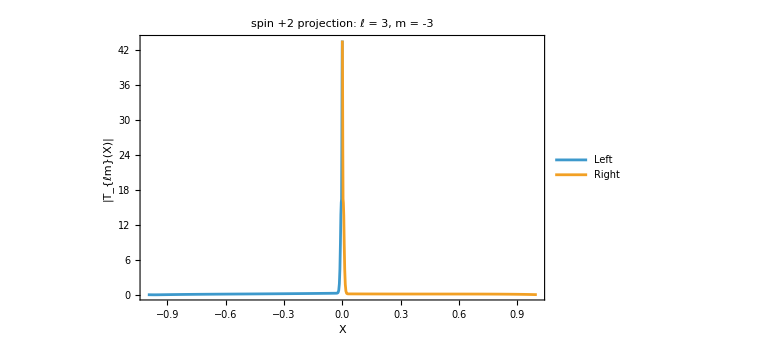

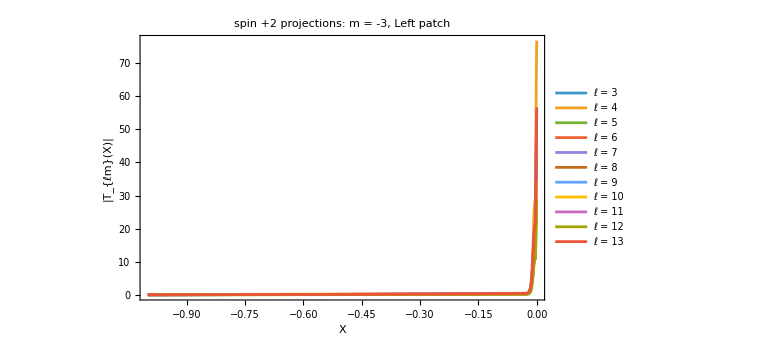

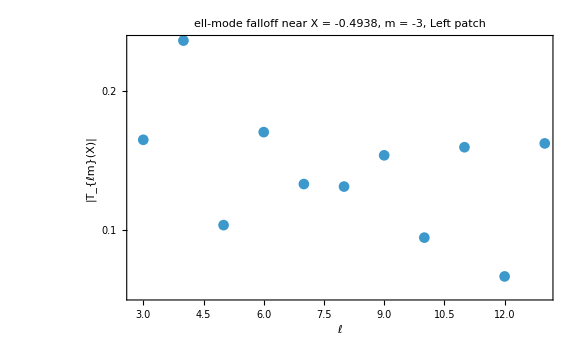

```mathematica
plus2Plots=makePlus2ProjectionPlots[plus2Run,"M"->-3,"Ell"->3,"Patch"->"Left","X0"->-0.5,"Transform"->Abs,"QuantityLabel"->"|T_{ℓm}(X)|","DisplayPlots"->True,"ExportPlots"->True];
```

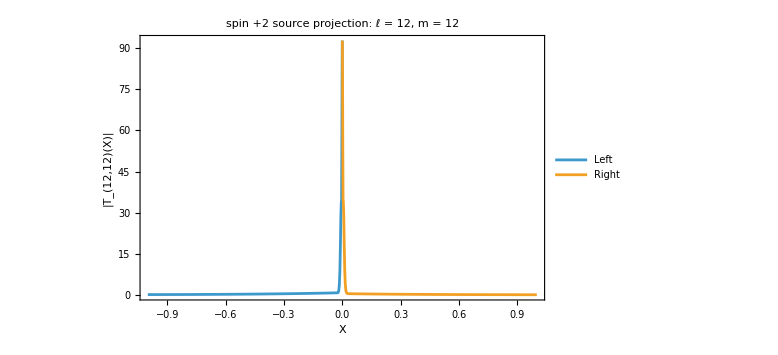

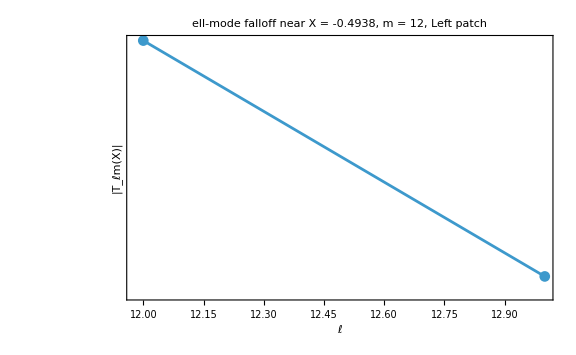
Only 2 ell values are available for m = 12: {12,13}. This is expected because ell >= |m|. Use a lower-|m| sector for a meaningful falloff test.
-Graphics-

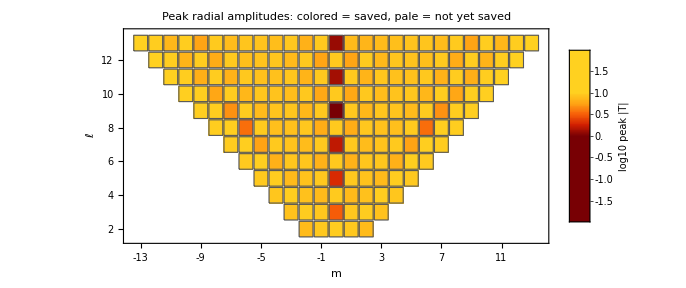

```mathematica
plotsM12=makePlus2DiagnosticPlots[plus2Run,"M"->12,"Ell"->12,"Patch"->"Left","X0"->-0.5];
```

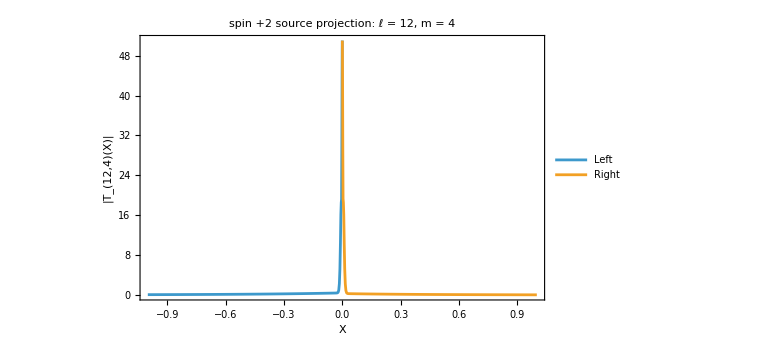

```mathematica
plus2RadialModePlot[plus2Run,4,12]
```

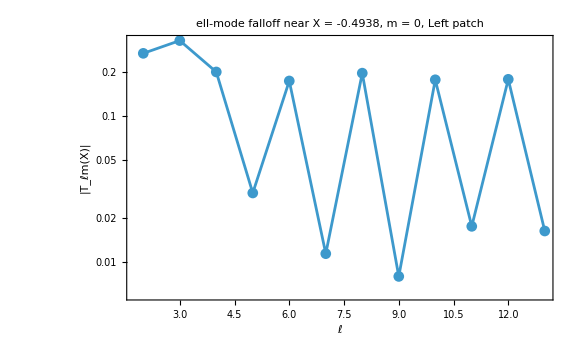

```mathematica
plus2EllFalloffPlot[plus2Run,"M"->0,"Patch"->"Left","X0"->-0.5]
```

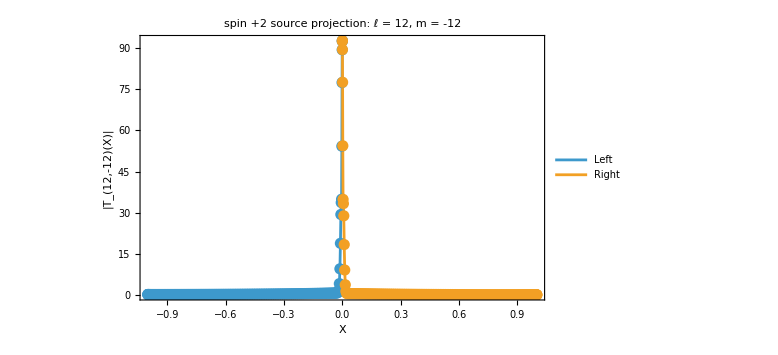

```mathematica
plus2RadialModePlot[plus2Run,-12,12]/. Line[data_]:>{Line[data],PointSize[0.014],Point[data]}
```

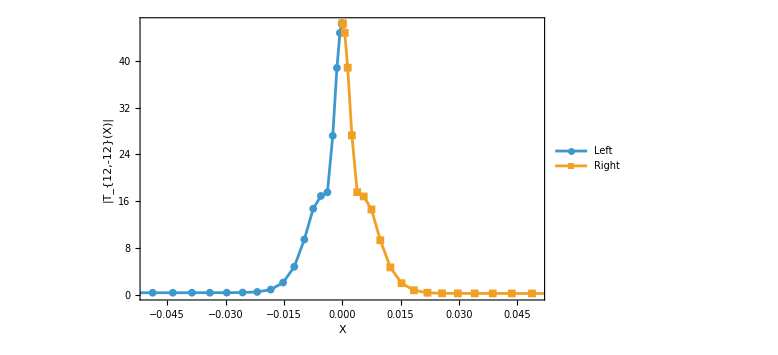

```mathematica
sector=plus2Run["Sectors"][-4];

ellList=sector["Metadata"]["ellList"];

ellPosition=First@FirstPosition[ellList,10];

leftValues=Abs[sector["ProjectionMatrices"]["Left"][[All,ellPosition]]];

rightValues=Abs[sector["ProjectionMatrices"]["Right"][[All,ellPosition]]];

ListLinePlot[{Transpose@{XLeftGridProd,leftValues},Transpose@{XRightGridProd,rightValues}},Joined->True,PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"X","|T_{12,-12}(X)|"},PlotLegends->{"Left","Right"},PlotRange->{{X0val-0.05,X0val+0.05},All},ImageSize->Large]
```

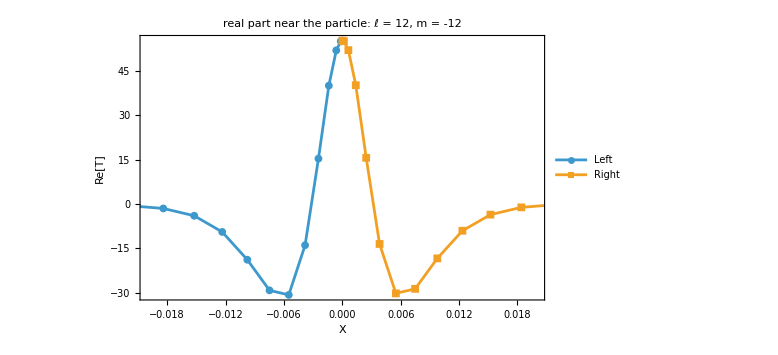
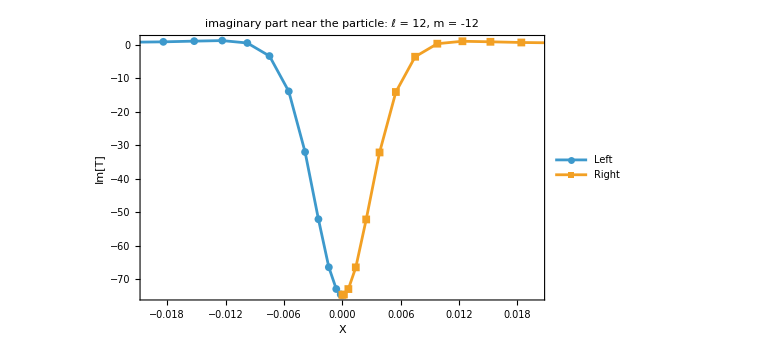

```mathematica
plotPlus2NearParticleComponents[plus2Run,-12,12,0.02]
```

```mathematica
comparison=plus2CompareStoredModes[plus2Run,{-2,3},{-12,12},"Left"];
```

```mathematica
comparison["Report"]//Dataset
```

```mathematica
ClearAll[plus2LocalSlopePlot];

plus2LocalSlopePlot[run_Association,m_Integer,ell_Integer]:=Module[{sector,ellList,ellPos,makeRows,makeSlopes},sector=run["Sectors"][m];
ellList=sector["Metadata"]["ellList"];
ellPos=First@FirstPosition[ellList,ell];
makeRows[patch_String]:=SortBy[Select[Transpose@{Abs[run["PatchAssoc"][patch]-X0val],Abs[sector["ProjectionMatrices"][patch][[All,ellPos]]]},#[[1]]>0&&#[[2]]>0&],First];
makeSlopes[patch_String]:=Module[{rows,logDistance,logValue},rows=makeRows[patch];
logDistance=Log[rows[[All,1]]];
logValue=Log[rows[[All,2]]];
Transpose@{Exp@MovingAverage[logDistance,2],Differences[logValue]/Differences[logDistance]}];
ListLogLinearPlot[{makeSlopes["Left"],makeSlopes["Right"]},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"|X - X0|","effective local slope"},PlotLabel->Row[{"local radial scaling: ","ℓ = ",ell,", m = ",m}],PlotLegends->{"Left","Right"},PlotRange->All,ImageSize->Large]];
```

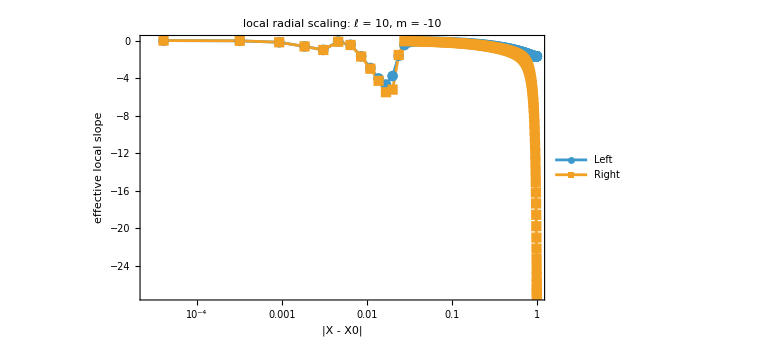

```mathematica
plus2LocalSlopePlot[plus2Run,-10,10]
```

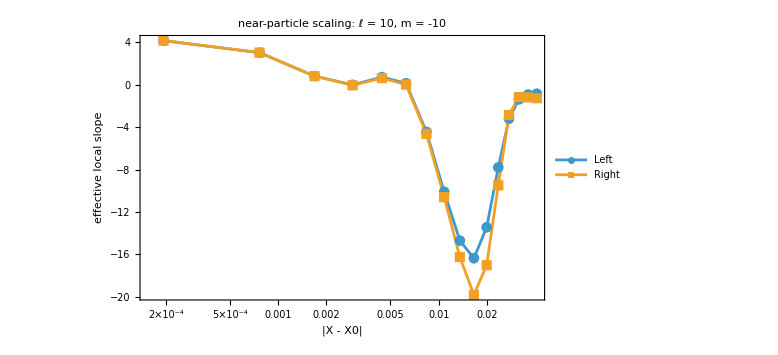

```mathematica
plus2LocalSlopePlotNearParticle[plus2Run,-10,10,"MaxDistance"->0.05,"MovingFitPoints"->4]
```

```mathematica
ClearAll[plus2InnermostSlopeTable];

plus2InnermostSlopeTable[run_Association,m_Integer,ell_Integer,n_Integer:8]:=Module[{sector,ellList,ellPos,makeRows,makeTable},sector=run["Sectors"][m];
ellList=sector["Metadata"]["ellList"];
ellPos=First@FirstPosition[ellList,ell];
makeRows[patch_String]:=SortBy[Select[Transpose@{Abs[run["PatchAssoc"][patch]-X0val],Abs[sector["ProjectionMatrices"][patch][[All,ellPos]]]},#[[1]]>0&&#[[2]]>0&],First];
makeTable[patch_String]:=Module[{rows,distances,values,slopes},rows=Take[makeRows[patch],UpTo[n+1]];
distances=rows[[All,1]];
values=rows[[All,2]];
slopes=Differences[Log[values]]/Differences[Log[distances]];
MapThread[<|"Patch"->patch,"RepresentativeDistance"->#1,"EffectiveSlope"->#2|>&,{Sqrt[Most[distances] Rest[distances]],slopes}]];
Dataset[Join[makeTable["Left"],makeTable["Right"]]]];
```

```mathematica
plus2InnermostSlopeTable[plus2Run,-10,10]
```